## Documentation

What this code does:  a) Imports simulation data output from the compiled c++ code ...\bin\simulate_reaches  b) Does post-processing on simulation data
c) creates data plots d) performs joint-fv calculations e) creates joint-fv animations 

Dependencies:  This code uses data stored in .../outputData/setN02_ALL

Warning:  
Copy the repository folder to your local system, but do not change the locations of the code or data files within that internal folder structure

References:
(1) Murtola, T., & Richards, C. (2022). The impact of intrinsic muscle properties on simulated reaching performance. Computer Methods in Biomechanics and Biomedical Engineering, 26(7), 777-788.
(2) Murtola, T., & Richards, C. (2023). The impact of age-related increase in passive muscle stiffness on simulated upper limb reaching. Royal Society open science, 10(2), 221453.

General abbreviations/prefixes used in this code:
FV - force-velocity relationship
sho - shoulder
elb - elbow
wri - wrist
flx - flexor
ext - extensor
frc - muscle force (N)
vel - muscle velocity (L/optimal length)
fvg - force-velocity gain
flg -force-length gain
act - muscle activation
qvel/acc - joint velocity/accel (radians...)
ctrl - muscle excitation data

Data structures:
xxxDATA  or xxxxDATA is N x 6 for muscle parameters (e.g. frc, vel) and N x 3 for joint parameters (e.g. qvel, qfrc); N = number of time points
xxxDATAsec or xxxDATAsec is Nx6x2 or Nx3x2 for xy pairs where x is time (s) and y is the value; N = number of time points
shofvDATA2D (also elbfv...; wrifv...) Nx1 of fv plot data (each element is one panel from Fig. 4 in the manuscript showing the joint fv trajectory at one point in time) ; N = number of time points

Indexing:
joint indexing: sho, elb, wri --> 1, 2, 3
muscle indexing: sho flexor, sho extensor, elb flexor, elb extensor... --> 1, 2, 3, 4 ...

e.g. time-series data for elbow flexor force = frcDATA[[;;, 3]];

time sampling: 
time samples are 0.002

Trial conditions (specified in trial name):
For detailed documentation see ...\doc\
and source code ...\inc\simulate_reaches.cpp

“A03_FB_P00_f0”
A03 = 3rd order activation dynamics (alt A01)
FB = feedback controlled (alt FF)
P00 = no perturbation (alt P01, P02, P03, P04 perturbations at different times)
f0 = fast speed reach target 0 (alt s0 or f1, f2 for slow speed or different reach targets, respectively)

For joint-fv manuscript, use the following trials:
“A03_FB_P00_f0” - control; forward reach target
“A03_FB_P00_f1” - control; sideways reach target
“A03_FB_P00_f2” - control; cross-body reach target
“A03_FB_P04_f0” - perturbation; forward reach target

Color coding:  black = shoulder; red = elbow; wrist = blue; solid = flexor; dashed = extensor

## Initialisation: Utility functions and constants

```mathematica
(*-------Muscle force-velocity functions and parameters used in Murtola & Richards, 2022/23-------*)
FVmurtola[vm_,vmax_,d1_,d2_,d3_]:=Module[{fvshort,fvlength},
fvshort=(1-vm/vmax)/(1+d1*vm/vmax);(*shortening portion*)
fvlength=d2-((d2-1)*(1+vm))/(1-d3*vm);
If[vm>0,fvshort,fvlength]
](*obselete function - use FVpiecewise instead*)

FVpiecewise[vmreal_,vmax_,d1_,d2_,d3_,offset_:0]:=Module[{fvshort,fvlength,vm},
vm=(vmreal+offset);
fvshort=(1-vm/vmax)/(1+d1*vm/vmax);(*shortening portion*)
fvlength=d2-((d2-1)*(1+vm/vmax))/(1-d3*vm/vmax);
Piecewise[{{fvshort,vm>=0},{fvlength,vm<0}}]
]

(*---parameters for muscles.  See Murtola & Richards 2022 for where these parameters came from----*)
fvparam={4,1.8,30.24};(*fv parameters - see see (1,2)*)
(*rValues={0.045,0.045,0.041,0.041,0.035,0.035};*)(*static moment arm values from MuJoCo geometry;*)
(*note correction to elbow flexor, 1/10/25*)
rValues={0.045,0.045,0.057,0.041,0.035,0.035};(*Murtola & Richards 2022; order corresponds to muscle indexing*)
optLengths={0.266872,0.298288,0.316149,0.440375,0.293339,0.317774};(*muscle optimal lengths used in Murtola & Richards, 2022/23 based on prior literature; order corresponds to muscle indexing*)
vmax=1.6;(*the value in ML/s used for Murtola & Richards 2022/23*)

(*set up the FV functions for agonist and antagonist*)
FV=FVpiecewise[vm,vmax,fvparam[[1]],fvparam[[2]],fvparam[[3]]];(*agonist*)
FVant=FVpiecewise[-vm,vmax,fvparam[[1]],fvparam[[2]],fvparam[[3]]];(*antagonist*)

(*agonist FV functions specific for joints, in angular velocity*)
FVsho=FVpiecewise[vm,vmaxrpsSho,fvparam[[1]],fvparam[[2]],fvparam[[3]]];
FVelb=FVpiecewise[vm,vmaxrpsElb,fvparam[[1]],fvparam[[2]],fvparam[[3]]];
FVwri=FVpiecewise[vm,vmaxrpsWri,fvparam[[1]],fvparam[[2]],fvparam[[3]]];

(*antagonist FV functions specific for joints, in angular velocity*)
FVantsho=FVpiecewise[-vm,vmaxrpsSho,fvparam[[1]],fvparam[[2]],fvparam[[3]]];
FVantelb=FVpiecewise[-vm,vmaxrpsElb,fvparam[[1]],fvparam[[2]],fvparam[[3]]];
FVantwri=FVpiecewise[-vm,vmaxrpsWri,fvparam[[1]],fvparam[[2]],fvparam[[3]]];

(*fmax values for muscles at joints, highest of flex/extensor; see (1)*)
shofmax=1500;
elbfmax=1300;
wrifmax=500;

(*assume muscles of each joint have same optimal lengths therefore same vmax in m/s*)
(*convert ML/s to rad/s given rvalues and averaged optimal lengths*)
mlps2rpsSho=Mean[optLengths[[{1,2}]]]/rValues[[1]];(*shoulder*)
mlps2rpsElb=Mean[optLengths[[{3,4}]]]/rValues[[3]];(*elbow*)
mlps2rpsWri=Mean[optLengths[[{5,6}]]]/rValues[[5]];(*wrist*)

(*vmax in radians per sec*)
vmaxrpsSho=vmax*mlps2rpsSho;
vmaxrpsElb=vmax*mlps2rpsElb;
vmaxrpsWri=vmax*mlps2rpsWri;

(*locations of the three reaching targets used - see (1)*)
targets={{0.15730,0.65,0},{0.55000,0.46,0},{-0.52000,0.3,0}};

(*-------utility function ---RESAMPLE DATA USING INTERPOLATION------*)
(*note - sometimes the output lenght is one less than desired depending on numerical roudning issues - if that's the case, just add one to the npoints output*)
dataResample[data1d_,npointsOutput_:100]:=Module[{datainterp,dataresampled},
datainterp=ListInterpolation[data1d];
dataresampled=Table[datainterp[t],{t,1,Length[data1d],(Length[data1d]-1)/(npointsOutput-1)}]
]

(*----plot style parameters-----*)

size=500;
font="Arial";
axthickness=(N@Round[Sqrt[size]])/8000;(*thickness of graph axes and ticks*)
graphstyle={FontFamily->font,FontSize->Round@Sqrt[size],FontColor->Black};


(*-----initialise file paths within github folder structure------*)
(*assuming folder structure is unchanged,get directory structure*)(*Load custom packages from the same folder**)dirScripts=NotebookDirectory[];
dirRoot=ParentDirectory[dirScripts];
dirPackages=FileNameJoin[Join[FileNameSplit[dirScripts],{"MathematicaPackages"}]];
AppendTo[$Path,dirPackages];(*add the github folder to the default path so packages can be loaded from there*)
dirmodel=dirRoot;
dirdata=FileNameJoin[{dirRoot,"/outputData"}];
dirreachingSims=FileNameJoin[{dirdata,"/setN02_ALL"}];
(*metadata=Import[dirreachingSims<>"reachingSims_metadata.xlsx","XLSX"][[1]][[2;;]];*)

Needs["FFmpegTools`"]
Needs["Biomechanics`"];
```

## Import time series data; generate time-series plots

Joint Angle (rad)

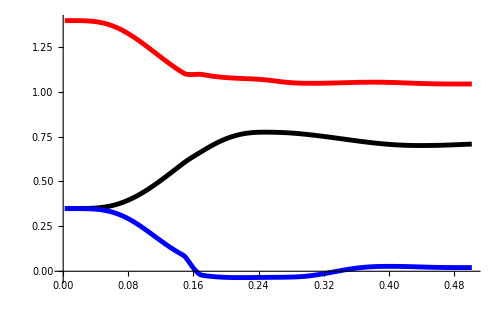

vel (v/vmax)

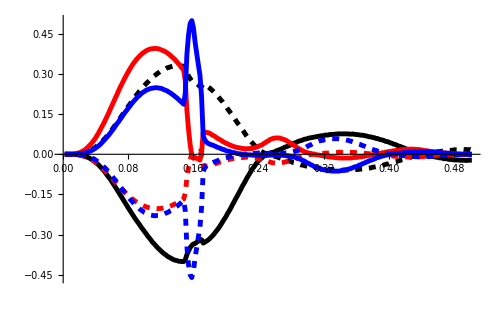

force (f/fmax)

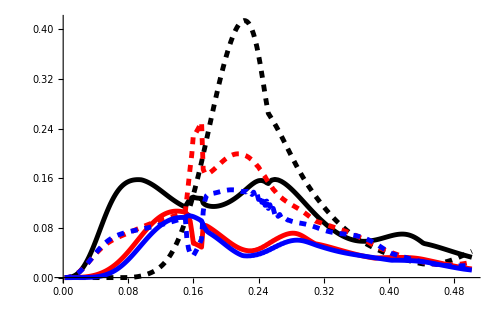

activation

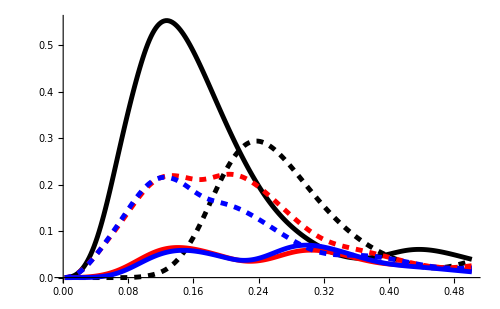

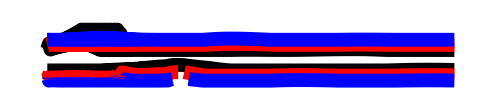

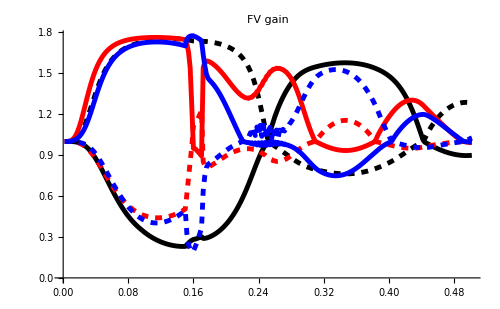

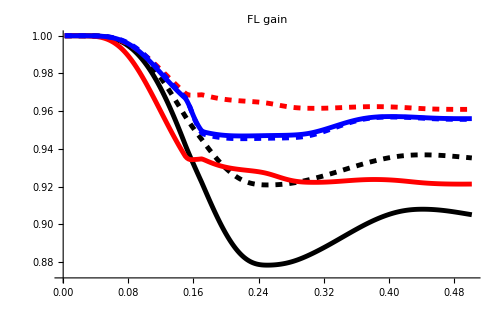

joint vel (rad/s)

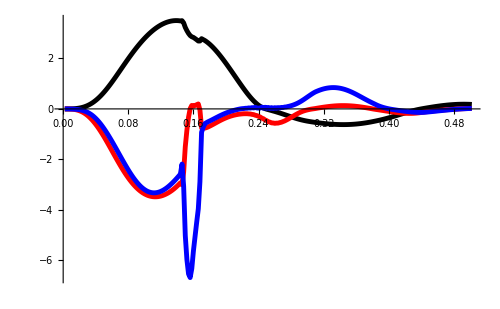

joint acc (rad/ss)

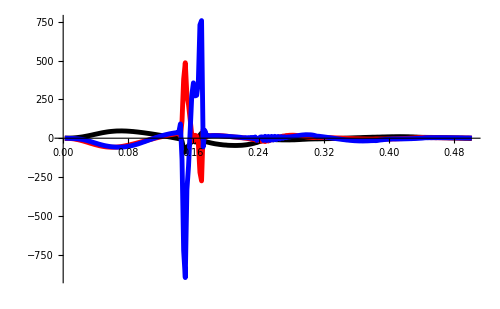

joint torques

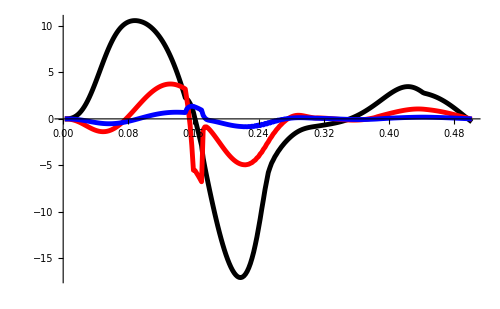

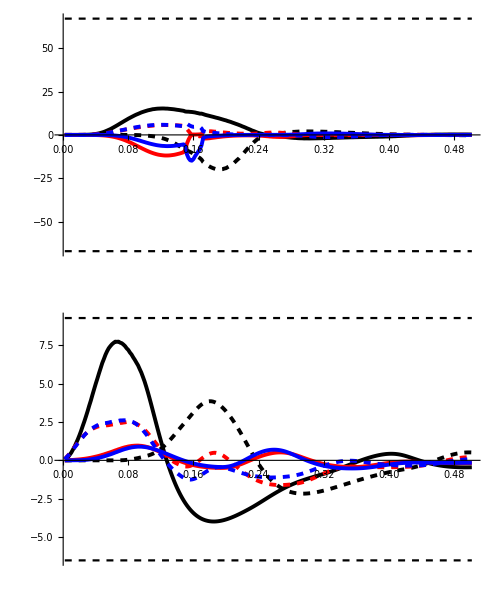

joint vel (rad/s)

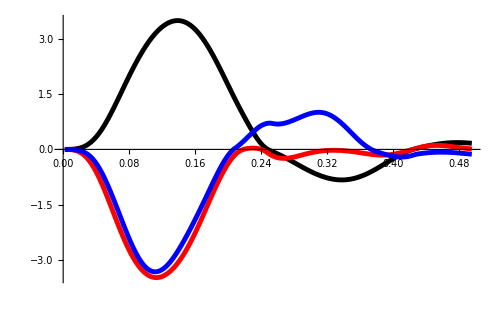

joint acc (rad/ss)

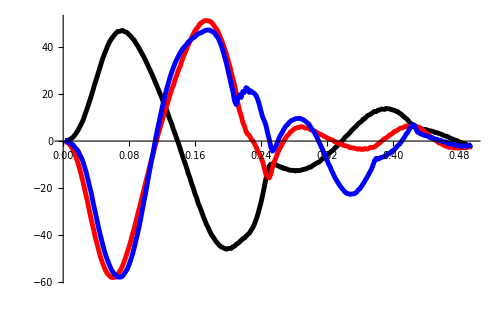

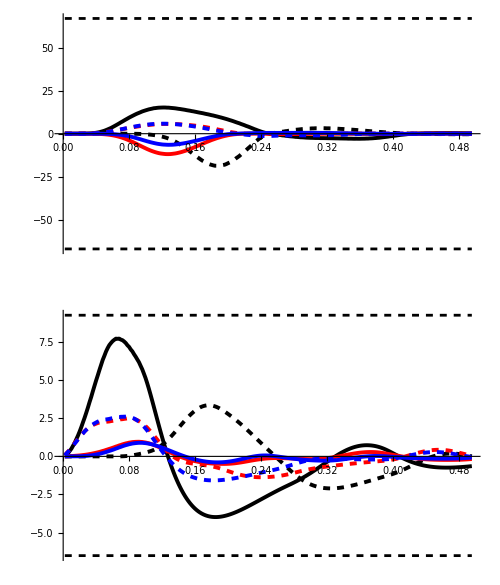

```mathematica
(*----------USER INPUT-----------*)
(*trialname="A03_FB_P00_f0";*)(*forward reach, control*)
trialname="A03_FB_P04_f0";(*forward reach, perturbation*)
(*trialname="A03_FB_P00_f1";*)(*sideways reach, control*)
(*trialname="A03_FB_P00_f2";*)(*cross-body reach, control*)
(*trialname="A03_FB_P01_f2";*)(*misc case, adjust as desired*)
(*------------------------------*)

(*--- parse trial name to load the appropriate trial condition----*)
inOutputData=False;(*if the trial is in the /outputData folder within MuJoCo folder*)
prefix=trialname<>"_";
trialnum=ToExpression[StringTake[trialname,-1]]+1;(*the reach target index*)
(*trialnum="1";*)
dirtrial=If[inOutputData,dirdata,dirreachingSims];
SetDirectory[dirtrial];

(*----extract cutoff index from metadata file----*)
(*load spreadsheet file with information about the final time of the reach (roughly when the arm stabilises)*)
(*If[!mostRecentQ,
trialrow=(Position[metadata[[;;,1]],trialname]//Flatten)[[1]]+ToExpression[trialnum];
cutoff=metadata[[trialrow,4]];
,
cutoff=-1
];*)
cutoffFile=prefix<>"cutoffData.csv";
cutoffData=Import[cutoffFile,"Data"];
cutoff=If[Length[Flatten[cutoffData]]==0,-1,cutoffData[[1,1]]];
cutoff=If[trialname=="A03_FB_P00_f2",300,cutoff];
(*cutoff=-1;*)
(*cutoff=400;*)(*for control condition - reach 0*)
(*cutoff=620;(*for control condition - reach 1*)*)
slice=1;;cutoff;

(*---- load coordinate data for reach targets------*)
targetXYZ=targets[[trialnum]];(*coordinates of reach targets*)
xyzFile=prefix<>"xyzOutput"<>".csv";
xyzDATA=Import[xyzFile,"Data"];

(*reaching error wrt target*)
errorData=Table[EuclideanDistance[Partition[xyzDATA[[i]],3][[-1]],targetXYZ],{i,1,Length[xyzDATA]}];
(*lastIndex=Flatten[Position[Threshold[errorData,0.0001],0.]][[1]];*)

(*----------set styles for time-series plots----------*)
colors={Black,Black,Red,Red,Blue,Blue};(*for muscle indexing*)
colors3={Black,Red,Blue};(*for joint indexing for plots with 3 lines instead of 6*)
plotthickness=0.007;
(*dashings={Thick,Dashed,Thick,Dashed,Thick,Dashed};*)
dashings={Thickness[plotthickness],{Dashed,Thickness[plotthickness]},Thickness[plotthickness],{Dashed,Thickness[plotthickness]},Thickness[plotthickness],{Dashed,Thickness[plotthickness]}};
dashings3={Thickness[plotthickness],Thickness[plotthickness],Thickness[plotthickness]};
styles=Thread[{colors,dashings}];
styles3=Thread[{colors3,dashings3}];


(*-------------misc constants-------------*)
mjdt=0.002;(*timestep set in MuJoCo simulation*)

(*parameters I've calculated for exploratory use and curiosity*)
maxActRate=9.26;(*max rate of activation*)
maxDeactRate=-6.51;(*max rate of deactivation*)
maxActDelta=maxActRate*mjdt;
maxDactDelta=maxDeactRate*mjdt;

(*----------generate filenames for importing data.  see documentation cell  for abbreviations---------*)
lenFile=prefix<>"lenOutput"<>".csv";
frcFile=prefix<>"frcOutput"<>".csv";
actFile=prefix<>"actOutput"<>".csv";
fvgFile=prefix<>"fvgOutput"<>".csv";
flgFile=prefix<>"flgOutput"<>".csv";
massFile=prefix<>"massOutput"<>".csv";
qposFile=prefix<>"qposOutput"<>".csv";
qfrcFile=prefix<>"qfrcOutput"<>".csv";
ctrlFile=prefix<>"ctrlOutput"<>".csv";
ctrqFile=prefix<>"ctrqOutput"<>".csv";

(*----------import raw data---*)
lenDATA=Import[lenFile,"Data"][[slice]];
frcDATA=-Import[frcFile,"Data"][[slice]];
actDATA=Import[actFile,"Data"][[slice]];
fvgDATA=Import[fvgFile,"Data"][[slice]];
flgDATA=Import[flgFile,"Data"][[slice]];
massDATA=Import[massFile,"Data"][[slice]];
qposDATA=Import[qposFile,"Data"][[slice]];
qfrcDATA=Import[qfrcFile,"Data"][[slice]];
ctrlDATA=Import[ctrlFile,"Data"][[slice]];
ctrqDATA=Import[ctrqFile,"Data"][[slice]];

timeData=Table[i*mjdt,{i,1,Length[lenDATA]}];

ResetDirectory[];

(*---process raw data with unit conversions, normalisations, etc. for convenience----*)
(*--- also, thread time series data with time points so data_sec are in x,y pairs as {time, value}  *)

(*normalize force data to get F/Fmax*)
fmaxValues={1500,1500,1300,1000,500,300};
(*max torque values*)
tmaxValues=fmaxValues*rValues;
(*force normalised by fmax*)
frcDATAn=Transpose[Table[frcDATA[[;;,i]]/fmaxValues[[i]],{i,1,6}]];


(*vel data in terms of optimal lengths per sec*)
frcDATAnRaw=frcDATAn;
frcDATAnsec=Transpose[Table[
frcdata=frcDATAnRaw[[;;,i]];
Thread[{timeData,frcdata}]
,{i,1,6}]];

(*in ML/s*)
velDATA=Transpose[Table[
ldata=lenDATA[[;;,i]];
straindata=1+(ldata-ldata[[1]])/optLengths[[i]];
veldata=Differentiator1D[straindata,mjdt]
,{i,1,6}]];

(*in m/s*)
velDATAmps=Transpose[Table[
ldata=lenDATA[[;;,i]];
straindata=1+(ldata-ldata[[1]])(*/optLengths[[i]]*);
veldata=Differentiator1D[straindata,mjdt]
,{i,1,6}]];(*vel data in meters per sec*)

(*in v/vmax*)
velDATAsec=Transpose[Table[
ldata=lenDATA[[;;,i]];
straindata=1+(ldata-ldata[[1]])/optLengths[[i]];
veldata=Differentiator1D[straindata,mjdt];
Thread[{timeData,veldata/vmax}]
,{i,1,6}]];

lenDATAsec=Transpose[Table[
ldata=lenDATA[[;;,i]];
straindata=1+(ldata-ldata[[1]])/optLengths[[i]];
Thread[{timeData,straindata}]
,{i,1,6}]];

actDATAraw=actDATA;
actDATAsec=Transpose[Table[
actdata=actDATAraw[[;;,i]];
Thread[{timeData,actdata}]
,{i,1,6}]];

fvgDATAraw=fvgDATA;
fvgDATAsec=Transpose[Table[
fvgdata=fvgDATAraw[[;;,i]];
Thread[{timeData,fvgdata}]
,{i,1,6}]];

flgDATAraw=flgDATA;
flgDATAsec=Transpose[Table[
flgdata=flgDATAraw[[;;,i]];
Thread[{timeData,flgdata}]
,{i,1,6}]];

(*joint velocities and accelerations*)
qvelDATA=Transpose[Table[
qdata=qposDATA[[;;,i]];
qveldata=Differentiator1D[qdata,mjdt]
,{i,1,3}]];

qvelDATAsec=Transpose[Table[
qdata=qposDATA[[;;,i]];
qveldata=Differentiator1D[qdata,mjdt];
Thread[{timeData,qveldata}]
,{i,1,3}]];

qaccDATA=Transpose[Table[
vdata=qvelDATAsec[[;;,i]];
accdata=Differentiator1D[vdata[[;;,2]],mjdt]
,{i,1,3}]];

qaccDATAsec=Transpose[Table[
vdata=qvelDATAsec[[;;,i]];
accdata=Differentiator1D[vdata[[;;,2]],mjdt];
Thread[{timeData,accdata}]
,{i,1,3}]];

(*mass matrix data*)
mmDATA=Table[Partition[massDATA[[i]],3],{i,1,Length[massDATA]}];

(*"length (m)"
plen=ListLinePlot[Transpose[lenDATA],PlotRange->All,PlotStyle->styles,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]*)

qposDATAraw=qposDATA;
qposDATAsec=Transpose[Table[
qposdata=qposDATAraw[[;;,i]];
Thread[{timeData,qposdata}]
,{i,1,3}]];

qfrcDATAraw=qfrcDATA;
qfrcDATAsec=Transpose[Table[
qfrcdata=qfrcDATAraw[[;;,i]];
Thread[{timeData,qfrcdata}]
,{i,1,3}]];

(*ctrlDATAraw=ctrlDATA;
ctrlDATA=Transpose[Table[
ctrldata=ctrlDATAraw[[;;,i]];
Thread[{timeData,ctrldata}]
,{i,1,6}]];*)

(*calculate muscle power (units not meaningful)- convention is shortening muscle--> positive power*)
pwrDATA=Transpose[Table[-velDATA[[;;,i]]*frcDATA[[;;,i]],{i,1,6}]];

(*calculate power in W/kg*)
(*estimate muscle volume*)
(*assume 20N/cm2*)
muscleCSAs=fmaxValues/20;(*in cm2*)
optLengthscm=optLengths*100;
musdensity=1.06;(*g/cm3*)
muscleVol=muscleCSAs*optLengthscm;(*in cm3*)
musmassValues=muscleVol*musdensity/1000(*estimated muscle mass in kg*);

pwrDATAwpkg=Transpose[Table[(-velDATAmps[[;;,i]]*frcDATA[[;;,i]])/musmassValues[[i]],{i,1,6}]];

pwrDATAwpkgsec=Transpose[Table[
pwrdata=pwrDATAwpkg[[;;,i]];
Thread[{timeData,pwrdata}]
,{i,1,6}]];

maxpwrValues=Table[0.3*fmaxValues[[i]]*(0.5*optLengths[[i]]),{i,1,Length[fmaxValues]}];
maxpwr=Max[maxpwrValues];

(*----------create time-series plots---------*)

ppwrRaw=ListLinePlot[pwrDATAwpkgsec//Transpose,PlotRange->All,PlotStyle->styles,BaseStyle->graphstyle];

ppwr=Show[
ListLinePlot[{{{timeData[[1]],maxpwr},{timeData[[-1]],maxpwr}},{{timeData[[1]],-maxpwr},{timeData[[-1]],-maxpwr}}},PlotStyle->{{Black,Dashed},{Black,Dashed}},BaseStyle->graphstyle],
ppwrRaw
];

dactDATAsec=Transpose[Table[
adata=actDATA[[;;,i]];
dadata=Differentiator1D[adata,mjdt];
Thread[{timeData,dadata}]
,{i,1,6}]];


pdactRaw=ListLinePlot[dactDATAsec//Transpose,PlotRange->All,PlotStyle->styles];

pdact=Show[
ListLinePlot[{{{timeData[[1]],maxActRate},{timeData[[-1]],maxActRate}},{{timeData[[1]],maxDeactRate},{timeData[[-1]],maxDeactRate}}},PlotStyle->{{Black,Dashed},{Black,Dashed}},BaseStyle->graphstyle],
pdactRaw
];

"Joint Angle (rad)"
pang=ListLinePlot[Transpose[qposDATAsec],PlotRange->All,PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]

(*"muscle length (m)"
plen=ListLinePlot[Transpose[lenDATAsec],PlotRange->All,PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]*)

"vel (v/vmax)"
pvel=ListLinePlot[Transpose[velDATAsec],PlotRange->All,PlotStyle->styles,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]

"force (f/fmax)"
pfrc=ListLinePlot[Transpose[frcDATAnsec],PlotRange->All,PlotStyle->styles,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]

"activation"
pact=ListLinePlot[Transpose[actDATAsec],PlotRange->All,PlotStyle->styles,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]

cols={colors[[1]],colors[[3]],colors[[5]]};
xplotsFlx=Show[
ListLinePlot[Transpose[ctrlDATA[[;;,1]]]+0,PlotStyle->{cols[[1]],Thickness[0.02]},PlotRange->{Automatic,{-2,2}},Axes->False,
BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness],AspectRatio->0.2],
ListLinePlot[Transpose[ctrlDATA[[;;,3]]]+0.25,PlotStyle->{cols[[2]],Thickness[0.02]},
BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]],
ListLinePlot[Transpose[ctrlDATA[[;;,5]]]+0.5,PlotStyle->{cols[[3]],Thickness[0.02]},
BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]
];

xplotsExt=Show[
ListLinePlot[Transpose[ctrlDATA[[;;,2]]]-1,PlotStyle->{cols[[1]],Thickness[0.02]},PlotRange->{Automatic,{-2,2}},Axes->False,
BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness],AspectRatio->0.2],
ListLinePlot[Transpose[ctrlDATA[[;;,4]]]-1.25,PlotStyle->{cols[[2]],Thickness[0.02]},
BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]],
ListLinePlot[Transpose[ctrlDATA[[;;,6]]]-1.5,PlotStyle->{cols[[3]],Thickness[0.02]},
BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]
];

xplots=Show[xplotsFlx,xplotsExt]



ListLinePlot[Transpose[fvgDATAsec],PlotRange->All,BaseStyle->graphstyle,PlotStyle->styles,PlotLabel->"FV gain"]
ListLinePlot[Transpose[flgDATAsec],PlotRange->All,BaseStyle->graphstyle,PlotStyle->styles,PlotLabel->"FL gain"]

"joint vel (rad/s)"
pqvel=ListLinePlot[Transpose[qvelDATAsec],PlotRange->All,PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]

"joint acc (rad/ss)"
pqacc=ListLinePlot[Transpose[qaccDATAsec],PlotRange->All,PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]

(*

"induced acc"
pqaccInduced=ListLinePlot[Table[Inverse[mmDATA[[i]]].{qfrcDATA[[i,1]],0,0},{i,1,Length[mmDATA]}]//Transpose,PlotStyle->{{Dashed,Black},{Red,Dashed},{Blue,Dashed}},PlotRange->All,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]
ListLinePlot[Table[Inverse[mmDATA[[i]]].{0,qfrcDATA[[i,2]],0},{i,1,Length[mmDATA]}]//Transpose,PlotStyle->{Black,Red,Blue},PlotRange->All]
ListLinePlot[Table[Inverse[mmDATA[[i]]].{0,0,qfrcDATA[[i,3]]},{i,1,Length[mmDATA]}]//Transpose,PlotStyle->{Black,Red,Blue},PlotRange->All]

*)
Print["joint torques"]
ptrq=ListLinePlot[Transpose[qfrcDATAsec],PlotRange->All,PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]]

range=1;
p1=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1}];
Manipulate[
points=Partition[xyzDATA[[i]],3];
p2=Graphics3D[Line[points]];
Show[p1,p2]
,{i,1,Length[xyzDATA],1}];

figurePlot=GraphicsColumn[{pang,pfrc,xplots,pvel,pqacc},ImageSize->500,ImagePadding->{{Automatic,Automatic},None}];
figurePlotb=GraphicsColumn[{ppwr,pdact},ImageSize->500,ImagePadding->{{Automatic,Automatic},None}]
```

-----OPTIONAL------Use this code below to create an interactive cell to animate the reach---------------------

```mathematica
range=1;
ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->Red,Axes->False,Boxed->False];
(*reachAnim=Table*)Manipulate[
points=Partition[xyzDATA[[i]],3];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4]
,{i,2,Length[xyzDATA[[;;cutoff]]],5}]
(*note starts at 2 to have same number of frames as jointFV animations*)
```

```mathematica
(*for exporting figure data*)
SetDirectory[dirreachingSims];
Export[trialname<>"_b.png",figurePlotb];
ResetDirectory[];
```

```mathematica
164./6000
```

0.0273333

```mathematica
(*for exporting animations as gif's*)
Export["reachAnim_fast_reach1.gif",reachAnim,"DisplayDurations"->0.08]
```

reachAnim_fast_reach1.gif

-------------------------------------------------------------------------------------------------------------------------------------------------------

## Compute joint-fv data; generate joint-fv plots (takes a while)

```mathematica
Clear[shofvDATA2D,elbfvDATA2D,wrifvDATA2D]
actScale=1.;(*defunct scaling term for code development - leave = 1 always*)

(*--allocate space for fv ceiling data (ceiling is the max value on joint-fv curve for given level of activation)--*)
fvceilingSho={};
fvceilingElb={};
fvceilingWri={};

(*--allocate space for joint-fv plots for all joints---*)
shofvDATA2D={};
elbfvDATA2D={};
wrifvDATA2D={};

(*--allocate space for joint-fv data for all joints; pos means position on joint-fv curve ---*)
shofvposDATA={};
elbfvposDATA={};
wrifvposDATA={};

(*--allocate space for position data on of antagonist muscle----*)
fvantposSho={};
fvantposElb={};
fvantposWri={};

(*plot styles*)
stylesFVcurves={{Black,Dashed},(*Darker[Darker[Green]]*)Gray,{Gray,Dashed}};

flON=False;(*turn on or off FL effects*)

(*--------------------------------------*)
(*---joint-fv computations for shoulder----*)
(*--------------------------------------*)
ijoint=1;
muscleSwap=1;(*make -1 if you want to swap agonist/antagonist*)
iMus={{1,2},{3,4},{5,6}}[[ijoint]];(*extract indices for flexor and extensor muscles*)
(*-- calculate muscle power for flexor and extensor during first 50 time samples---*)
(*--the muscle that generates most power first is the "dominant" muscle therefore defined as the agonist*)
(*this ant/ag designation will remain constant through the trial*)
meanpwrFlx=Mean[pwrDATA[[1;;50,iMus[[1]]]]];(*avg power for flexor*)
meanpwrExt=Mean[pwrDATA[[1;;50,iMus[[2]]]]];(*avg power for extensor*)
powerPoints={meanpwrFlx,meanpwrExt};
imax=Ordering[powerPoints,muscleSwap*-1][[1]];(*indicies that allow the ordering of flexor/extensor values based on their values*)
imin=Ordering[powerPoints,muscleSwap*1][[1]];
a=tmaxValues[[iMus]][[imin]]/tmaxValues[[iMus]][[imax]];(*this ratio determines how much to scale antagonist - i.e. we need to account for different muscle fmax values to weight their contributions to the joint-fv curve*)
shofvActLimitDATA={};
Do[
testtime=itr(*200*);
tmaxAg=tmaxValues[[iMus[[1]]]];(*max torque for flexor*)
tmaxAnt=tmaxValues[[iMus[[2]]]];(*max torque for extensor*)
(*a=tmaxAnt/tmaxAg;(*how much to scale antagonist*)*)
(*maxactIndex=Ordering[actDATA[[;;,iMus]],-1][[1]];*)(*4.6.2024 index when max activation reached*)
actPoints=actScale*actDATA[[testtime,iMus]];
flgPoints=flgDATA[[testtime,iMus]];
fvgPoints=fvgDATA[[testtime,iMus]];
asho=a;(*activation ratio for shoulder - for checking/debugging purposes*)
actMax=actPoints[[imax]](*Max[actPoints]*);
actMin=actPoints[[imin]](*Min[actPoints]*);
(*account for FL affects*)
flgMax=If[flON,flgPoints[[imax]],1];
flgMin=If[flON,flgPoints[[imin]],1];
fvgMax=fvgPoints[[imax]];
fvgMin=fvgPoints[[imin]];

actangle=Pi*(1-actMax);(*defunct line*)
velPoints=velDATA[[testtime,iMus]];
(*velPointsMean=Sign[velPoints]*Mean[Abs[velPoints]];(*they're not exaclty mirrored, so take average*);*)
(*velpos=Abs[velPointsMean[[1]]];*)(*vm coordinate on FV curve*)
velpos=-velPoints[[imax]]*mlps2rpsSho;(*convert X coordinate to rad/s*)
(*vm coordinate on FV curve- must be negated because shortening velocity is negative*)

(*fvceiling=flgMax*actMax*(FV/.vm->velpos)/.vm->velpos;*)
(*highest point in FV volume for that act level*)
fvceiling=flgMax*fvgMax*actMax;
fvceilingSho=Join[fvceilingSho,{fvceiling}];
(*fvantpos=flgMin*actMin*(FVant/.vm->velpos)/.vm->velpos;*)
fvantpos=flgMin*fvgMin*actMin;
(*point on lower activated muscle's FV curve*)
fvantposSho=Join[fvantposSho,{fvantpos}];
fvpos={velpos,0,fvceiling-a*fvantpos};(*joint operating point in joint FV volume*)

(*-------------------------------------------------------------------------------------------------------------*)

(*----save 2D fv plot data before making it 3D---*)
shofvposDATA=Join[shofvposDATA,{fvpos[[{1,3}]]}];
pointcol={Black,Red,Blue}[[1]];
pointsize=0.03;
jointFVsho={vm,0,FVsho};(*UNUSED*)
jointFVantsho={vm,0,FVantsho};(*UNUSED*)
jointFVscaled=jointFVsho;(*UNUSED*)
jointFVscaled[[3]]=actPoints[[imax]]*FVsho;(*top curve*)
jointFVantScaled=jointFVantsho;(*UNUSED*)
jointFVantScaled[[3]]=actPoints[[imax]]*FVsho-a*actPoints[[imin]]*FVantsho;(*middle curve*)
jointFVantScaledMax=jointFVantsho;(*UNUSED*)
jointFVantScaledMax[[3]]=actPoints[[imax]]*FVsho-a*Max[actPoints]*FVantsho;(*UNUSED bottom curve*)
jointFVantScaledMaxalt=-a*actPoints[[imin]]*FVantsho;(*bottom curve*)
plotfv2D=Show[
Plot[{jointFVscaled[[3]],jointFVantScaled[[3]],(*jointFVantScaledMax[[3]]*)jointFVantScaledMaxalt},{vm,-vmaxrpsSho,vmaxrpsSho},PlotRange->{-2*Max[actDATA],2*Max[actDATA](*-5,5*)},AspectRatio->1,PlotStyle->stylesFVcurves],
ListPlot[{shofvposDATA[[-1]]},PlotStyle->pointcol],
ListPlot[shofvposDATA,PlotStyle->{pointcol,Opacity[0.2]}]
];
shofvDATA2D=Join[shofvDATA2D,{plotfv2D}];
(*---------------------------------------------*)

(*to rotate it into the visualisation volume*)
(*fvposr=fvTransform[fvpos]*)
,{itr,1,Length[actDATA]}];

(*--------------------------------------*)
(*---joint-fv computations for elbow-------*)
(*--------------------------------------*)

ijoint=2;
muscleSwap=1;(*make -1 if you want to swap agonist/antagonist*)
iMus={{1,2},{3,4},{5,6}}[[ijoint]];
meanpwrFlx=Mean[pwrDATA[[1;;50,iMus[[1]]]]];
meanpwrExt=Mean[pwrDATA[[1;;50,iMus[[2]]]]];
powerPoints={meanpwrFlx,meanpwrExt};
imax=Ordering[powerPoints,muscleSwap*-1][[1]];
imin=Ordering[powerPoints,muscleSwap*1][[1]];
a=tmaxValues[[iMus]][[imin]]/tmaxValues[[iMus]][[imax]];(*how much to scale antagonist*)
elbfvActLimitDATA={};
Do[
testtime=itr(*200*);
tmaxAg=tmaxValues[[iMus[[1]]]];(*max torque for flexor*)
tmaxAnt=tmaxValues[[iMus[[2]]]];(*max torque for extensor*)
(*a=tmaxAnt/tmaxAg;*)(*how much to scale antagonist*)
(*maxactIndex=Ordering[actDATA[[;;,iMus]],-1][[1]];*)(*4.6.2024 index when max activation reached*)
actPoints=actScale*actDATA[[testtime,iMus]];
flgPoints=flgDATA[[testtime,iMus]];
fvgPoints=fvgDATA[[testtime,iMus]];

aElb=a;(*activation ratio for elbow*)

actMax=actPoints[[imax]](*Max[actPoints]*);
actMin=actPoints[[imin]](*Min[actPoints]*);
(*account for FL affects*)
flgMax=If[flON,flgPoints[[imax]],1];
flgMin=If[flON,flgPoints[[imin]],1];
fvgMax=fvgPoints[[imax]];
fvgMin=fvgPoints[[imin]];

actangle=Pi*(1-actMax);
velPoints=velDATA[[testtime,iMus]];
(*velPointsMean=Sign[velPoints]*Mean[Abs[velPoints]];(*they're not exaclty mirrored, so take average*);
velpos=Abs[velPointsMean[[1]]]*mlps2rpsElb;(*vm coordinate on FV curve*)*)
velpos=-velPoints[[imax]]*mlps2rpsElb;
(*velpos=-qvelDATA[[testtime,ijoint]];*)(*Change - 1.10.25 joint velocity*)
(*velpos=-Sign[velPoints[[imax]]]*Mean[Abs[velPoints]]*mlps2rpsElb;*)(*average because moment arms are different*)
(*velpos=Sign[velPoints[[imax]]]*qvelDATAsec[[testtime,ijoint,2]];*)(*joint velocity*)
(*vm coordinate on FV curve- must be negated because shortening velocity is negative*)

(*fvceiling=flgMax*actMax*(FV/.vm->velpos)/.vm->velpos;*)
(*highest point in FV volume for that act level*)
fvceiling=flgMax*fvgMax*actMax;
fvceilingElb=Join[fvceilingElb,{fvceiling}];
(*fvantpos=flgMin*actMin*(FVant/.vm->velpos)/.vm->velpos;*)
fvantpos=flgMin*fvgMin*actMin;
(*point on lower activated muscle's FV curve*)
fvantposElb=Join[fvantposElb,{fvantpos}];
fvpos={velpos,0,fvceiling-a*fvantpos};(*joint operating point in joint FV volume*)
(*fvTransform=RotationTransform[actangle,{0,0,1},anchor];*)


(*-------------------------------------------------------------------------------------------------------------*)

(*----save 2D fv plot data before making it 3D---*)
elbfvposDATA=Join[elbfvposDATA,{fvpos[[{1,3}]]}];
pointcol={Black,Red,Blue}[[1]];
pointsize=0.03;
jointFVelb={vm,0,FVelb};
jointFVantelb={vm,0,FVantelb};
jointFVscaled=jointFVelb;
jointFVscaled[[3]]=actPoints[[imax]]*FVelb;
jointFVantScaled=jointFVantelb;
jointFVantScaled[[3]]=actPoints[[imax]]*FVelb-a*actPoints[[imin]]*FVantelb;
jointFVantScaledMax=jointFVantelb;
jointFVantScaledMax[[3]]=actPoints[[imax]]*FVelb-a*Max[actPoints]*FVantelb;
jointFVantScaledMaxalt=-a*actPoints[[imin]]*FVantelb;
plotfv2D=Show[
Plot[{jointFVscaled[[3]],jointFVantScaled[[3]],(*jointFVantScaledMax[[3]]*)jointFVantScaledMaxalt},{vm,-vmaxrpsElb,vmaxrpsElb},PlotRange->{-2*Max[actDATA],2*Max[actDATA](*-5,5*)},AspectRatio->1,PlotStyle->stylesFVcurves],
ListPlot[{elbfvposDATA[[-1]]},PlotStyle->pointcol],
ListPlot[elbfvposDATA,PlotStyle->{pointcol,Opacity[0.2]}]
];
elbfvDATA2D=Join[elbfvDATA2D,{plotfv2D}];
(*---------------------------------------------*)

(*to rotate it into the visualisation volume*)
(*fvposr=fvTransform[fvpos]*)
,{itr,1,Length[actDATA]}];


(*--------------------------------------*)
(*---joint-fv computations for wrist-------*)
(*--------------------------------------*)

ijoint=3;
muscleSwap=1;(*make -1 if you want to swap agonist/antagonist*)
iMus={{1,2},{3,4},{5,6}}[[ijoint]];
meanpwrFlx=Mean[pwrDATA[[1;;50,iMus[[1]]]]];
meanpwrExt=Mean[pwrDATA[[1;;50,iMus[[2]]]]];
powerPoints={meanpwrFlx,meanpwrExt};
imax=Ordering[powerPoints,muscleSwap*-1][[1]];
imin=Ordering[powerPoints,muscleSwap*1][[1]];
a=tmaxValues[[iMus]][[imin]]/tmaxValues[[iMus]][[imax]];(*how much to scale antagonist*)

wrifvActLimitDATA={};
Do[
testtime=itr(*200*);
tmaxAg=tmaxValues[[iMus[[1]]]];(*max torque for flexor*)
tmaxAnt=tmaxValues[[iMus[[2]]]];(*max torque for extensor*)
(*a=tmaxAnt/tmaxAg;(*how much to scale antagonist*)*)
(*maxactIndex=Ordering[actDATA[[;;,iMus]],-1][[1]];*)(*4.6.2024 index when max activation reached*)
actPoints =actScale*actDATA[[testtime,iMus]];
flgPoints=flgDATA[[testtime,iMus]];
fvgPoints=fvgDATA[[testtime,iMus]];

(*rather than defining agonist/antagonist based on activation, do it based on producing positive power*)
(*take first chunk of data, see which muscle is producing positive power*)
(*this ant/ag designation will remain constant through the trial*)

awri=a;(*activation ratio for wrist*)
actMax=actPoints[[imax]](*Max[actPoints]*);
actMin=actPoints[[imin]](*Min[actPoints]*);
(*account for FL affects*)
flgMax=If[flON,flgPoints[[imax]],1];
flgMin=If[flON,flgPoints[[imin]],1];
fvgMax=fvgPoints[[imax]];
fvgMin=fvgPoints[[imin]];

actangle=Pi*(1-actMax);
velPoints=velDATA[[testtime,iMus]];
(*velPointsMean=Sign[velPoints]*Mean[Abs[velPoints]];(*they're not exaclty mirrored, so take average*);*)
(*velpos=Abs[velPointsMean[[1]]];*)(*vm coordinate on FV curve*)
velpos=-velPoints[[imax]]*mlps2rpsWri;(*vm coordinate on FV curve- must be negated because shortening velocity is negative*)

(*fvceiling=flgMax*actMax*(FV/.vm->velpos)/.vm->velpos;*)
(*highest point in FV volume for that act level*)
fvceiling=flgMin*fvgMax*actMax;
fvceilingWri=Join[fvceilingWri,{fvceiling}];
(*fvantpos=flgMin*actMin*(FVant/.vm->velpos)/.vm->velpos;*)
fvantpos=flgMin*fvgMin*actMin;
(*point on lower activated muscle's FV curve*)
fvantposWri=Join[fvantposWri,{fvantpos}];
fvpos={velpos,0,fvceiling-a*fvantpos};(*joint operating point in joint FV volume*)
(*fvTransform=RotationTransform[actangle,{0,0,1},anchor];*)

(*-------------------------------------------------------------------------------------------------------------*)

(*----save 2D fv plot data before making it 3D---*)
wrifvposDATA=Join[wrifvposDATA,{fvpos[[{1,3}]]}];
pointcol={Black,Red,Blue}[[1]];
pointsize=0.03;
jointFVwri={vm,0,FVwri};
jointFVantwri={vm,0,FVantwri};
jointFVscaled=jointFVwri;
jointFVscaled[[3]]=actPoints[[imax]]*FVwri;
jointFVantScaled=jointFVantwri;
jointFVantScaled[[3]]=actPoints[[imax]]*FVwri-a*actPoints[[imin]]*FVantwri;
jointFVantScaledMax=jointFVantwri;
jointFVantScaledMax[[3]]=actPoints[[imax]]*FVwri-a*Max[actPoints]*FVantwri;
jointFVantScaledMaxalt=-a*actPoints[[imin]]*FVantwri;
plotfv2D=Show[
Plot[{jointFVscaled[[3]],jointFVantScaled[[3]],(*jointFVantScaledMax[[3]]*)jointFVantScaledMaxalt},{vm,-vmaxrpsWri,vmaxrpsWri},PlotRange->{-2*Max[actDATA],2*Max[actDATA](*-5,5*)},AspectRatio->1,PlotStyle->stylesFVcurves],
ListPlot[{wrifvposDATA[[-1]]},PlotStyle->pointcol],
ListPlot[wrifvposDATA,PlotStyle->{pointcol,Opacity[0.2]}]
];
wrifvDATA2D=Join[wrifvDATA2D,{plotfv2D}];
(*---------------------------------------------*)

(*to rotate it into the visualisation volume*)
(*fvposr=fvTransform[fvpos]*)
,{itr,1,Length[actDATA]}];

yrange=(*0.05*)(*0.75*)0.5;
(*timings of the perturbation - absolute times vary because the have been triggered in relative times*)
pertTimings={
{"A03_FB_P01_f0",0.022},{"A03_FB_P02_f0",0.064},{"A03_FB_P03_f0",0.106},{"A03_FB_P04_f0",0.148},
{"A03_FB_P01_f1",0.032},{"A03_FB_P02_f1",0.094},{"A03_FB_P03_f1",0.158},{"A03_FB_P04_f1",0.222},
{"A03_FB_P01_f2",0.038},{"A03_FB_P02_f2",0.116},{"A03_FB_P03_f2",0.192},{"A03_FB_P04_f2",0.270}
};
(*perturbation never happens for controls, so make start time arbitrarily large*)
pertTimingsControl={{"A03_FB_P00_f0",10},{"A03_FB_P00_f1",10},{"A03_FB_P00_f2",10}};
pertTimings=Join[pertTimings,pertTimingsControl];
pertStart=pertTimings[[Position[pertTimings,trialname][[1,1]]]][[2]];
pertEnd=pertStart+0.018;
```

```mathematica
(*------------------------------------------------------*)
(*---interactive cell for animating joint fv trajectories---*)
(*------------------------------------------------------*)
range=1;
ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->Red,Axes->False,Boxed->False];
(*reachAnim=Table*)

Manipulate[
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->label];
GraphicsRow[{plot1,plot2},ImageSize->800]


,{fr,1,Length[shofvDATA2D],1},{joint,1,3,1}]
```

```mathematica
(*------------------------------*)
(*---export the jointfv data----*)
(*------------------------------*)
SetDirectory[dirMSdata];(*as defined in ReachingLimitsFigures.nb*)
Export["shofvposDATA_"<>trialname<>".csv",shofvposDATA]
Export["elbfvposDATA_"<>trialname<>".csv",elbfvposDATA]
Export["wrifvposDATA_"<>trialname<>".csv",wrifvposDATA]
ResetDirectory[];
```

wrifvposDATA_A03_FB_P04_f0.csv

```mathematica
(*---------------------------------------------*)
(*---------------------------------------------*)
(*---------------------------------------------*)
(*---------------------------------------------*)
(*-----ANALYSE COMPONENTS OF dTORQUE/dt--------*)
(*---------------------------------------------*)
(*----note: much of this is exploratory and-----*)
(*-----hypothetical, but some parameters are----*)
(*-----needed to generate the figure about------*)
(*------torque rates and activation rates-------*)
(*---------------------------------------------*)
```

3

dtorque Limits

positive dtorque limits: flexor, extensor

{493.558,379.66}

negative dtorque limit

{-726.643,-760.468}

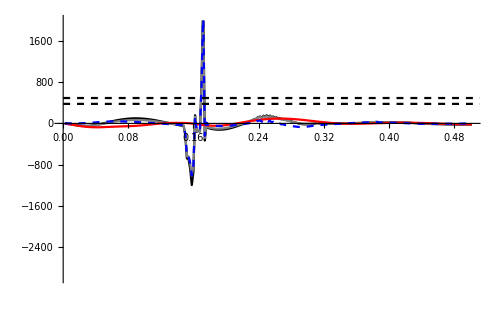

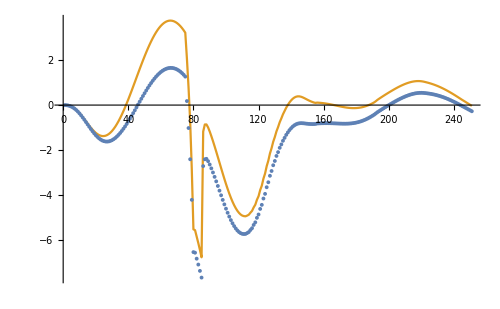

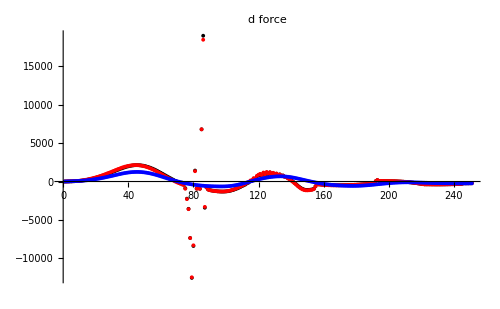

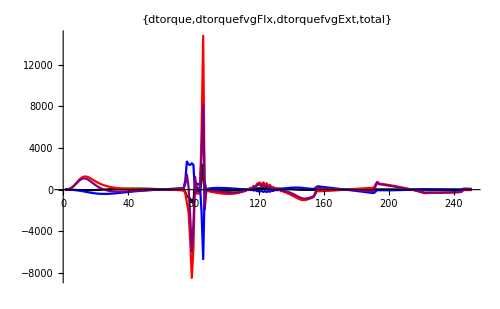

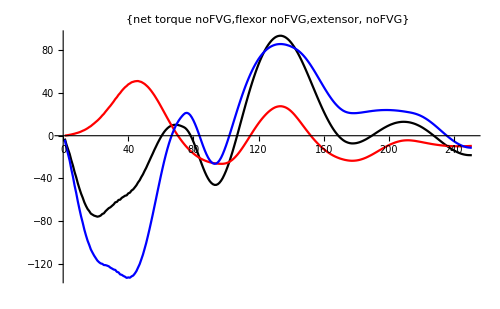

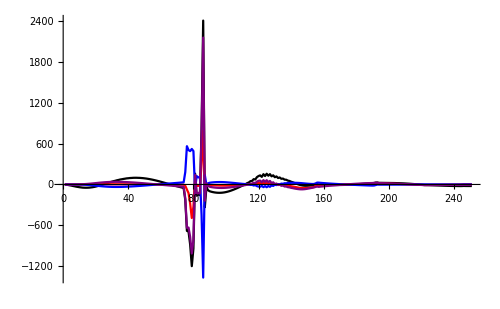

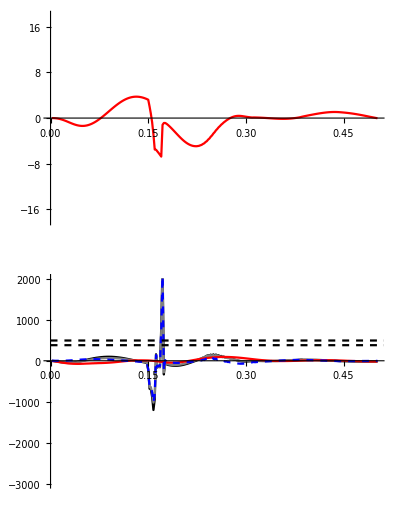

```mathematica
jntindex=2;(*1 = sho; 2 = elbow; 3 = wrist*)
prange={-6,10};(*y value range for plotting*)
flexOrExt=0;(*0 for flex 1 for ext*)
index=(jntindex-1)+jntindex+flexOrExt;(*index of the relevant muscle*)

(*activation data for Flx, Ext*)
adataFlx=actDATA[[;;,index]];
adataExt=actDATA[[;;,index+1]];

(*flg data for Flx, Ext*)
flgFlx=flgDATA[[;;,index]];
flgExt=flgDATA[[;;,index+1]];

(*fvg data for Flx, Ext*)
fvgFlx=fvgDATA[[;;,index]];
fvgExt=fvgDATA[[;;,index+1]];

(*muscle vel data for Flx, Ext*)
vdataFlx=velDATA[[;;,index]];
vdataExt=velDATA[[;;,index+1]];

(*moment arm data for Flx, Ext*)
rflx=rValues[[index]];
rext=rValues[[index+1]];

(*derivatives of the above*)
dadataFlx=1*Differentiator1D[adataFlx,mjdt];
dadataExt=1*Differentiator1D[adataExt,mjdt];

dflgFlx=1*Differentiator1D[flgFlx,mjdt];
dflgExt=1*Differentiator1D[flgExt,mjdt];

dfvgFlx=1*Differentiator1D[fvgFlx,mjdt];
dfvgExt=1*Differentiator1D[fvgExt,mjdt];

(*-----------------------------------------------------------------------------*)
(*mostly unused calculations for curiosity, pending further analysis and checking*)
(*-----------------------------------------------------------------------------*)
tqmax=tmaxValues[[jntindex]];
fmaxFlx=fmaxValues[[index]];
fmaxExt=fmaxValues[[index+1]];
(*c=qfrcDATA[[;;,jntindex]];*)
fdataFlx=frcDATA[[;;,index]];
fdataExt=frcDATA[[;;,index+1]];
dfdataFlx=Differentiator1D[fdataFlx,mjdt];
dfdataExt=Differentiator1D[fdataExt,mjdt];

dfdataFlxCal=flgFlx*fvgFlx*dadataFlx+adataFlx*fvgFlx*dflgFlx+adataFlx*flgFlx*dfvgFlx;
dfdataExtCal=flgExt*fvgExt*dadataExt+adataExt*fvgExt*dflgExt+adataExt*flgExt*dfvgExt;

ddataFlxCalnofvg=1*1*dadataFlx+adataFlx*fvgFlx*0+adataFlx*flgFlx*0;
ddataExtCalnofvg=1*1*dadataExt+adataExt*fvgExt*0+adataExt*flgExt*0;

ddataFlxCalnoact=flgFlx*fvgFlx*dadataFlx*0+adataFlx*fvgFlx*dflgFlx*0+adataFlx*flgFlx*dfvgFlx;
ddataExtCalnoact=flgExt*fvgExt*dadataExt*0+adataExt*fvgExt*dflgExt*0+adataExt*flgExt*dfvgExt;

dtorqueCal=fmaxFlx*rflx*dfdataFlxCal-fmaxExt*rext*dfdataExtCal;
Print["dtorque Limits"]
Print["positive dtorque limits: flexor, extensor"]
dtorqueLimitPos={fmaxFlx*rflx*maxActRate,fmaxExt*rext*maxActRate}
Print["negative dtorque limit"]
dtorqueLimitNeg={fmaxFlx*rflx*maxDeactRate-fmaxExt*rext*maxActRate,fmaxExt*rext*maxDeactRate-fmaxFlx*rflx*maxActRate}
dtorqueCaloFVGflx=fmaxFlx*rflx*ddataFlxCalnofvg;
dtorqueCaloFVGext=fmaxExt*rext*ddataExtCalnofvg;
dtorqueCalNoFVG=dtorqueCaloFVGflx-dtorqueCaloFVGext;
dtorqueFVGflx=fmaxFlx*rflx*dfvgFlx;
dtorqueFVGext=fmaxExt*rext*dfvgExt;
dtorqueCalFVG=dtorqueFVGflx+dtorqueFVGext;
dtorqueCalNoACT=fmaxFlx*rflx*ddataFlxCalnoact-fmaxExt*rext*ddataExtCalnoact;
tdata=qfrcDATA[[;;,jntindex]];

dtorque=Differentiator1D[tdata,mjdt];

torqueXY=Thread[{timeData,tdata}];
dtorqueXY=Thread[{timeData,dtorque}];
dtorqueCalXY=Thread[{timeData,dtorqueCal}];
dtorqueCalNoFVGXY=Thread[{timeData,dtorqueCalNoFVG}];
dtorqueCalNoACTXY=Thread[{timeData,dtorqueCalNoACT}];

(*-----------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------*)

(*create unformatted plots for inspection - these figures are for curiosity not publication*)
(*further mathematical analysis/confirmation is needed*)

Show[
p1=ListLinePlot[{dtorqueXY,dtorqueCalXY,dtorqueCalNoFVGXY,dtorqueCalNoACTXY},PlotStyle->{Black,Gray,Red,{Blue,Dashed}},PlotRange->{Automatic,{-3000,2000}},PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]],
p1a=ListLinePlot[{{0,dtorqueLimitPos[[1]]},{cutoff,dtorqueLimitPos[[1]]}},PlotStyle->{Black,Dashed}],
p1b=ListLinePlot[{{0,dtorqueLimitPos[[2]]},{cutoff,dtorqueLimitPos[[2]]}},PlotStyle->{Black,Dashed}]
]
ListPlot[{fdataFlx*rflx-fdataExt*rext,tdata},Joined->{False,True}]
ListPlot[{dfdataFlx,fmaxFlx*dfdataFlxCal,fmaxFlx*ddataFlxCalnofvg},PlotStyle->{Black,Red,Blue},PlotRange->All,PlotLabel->"d force"]
ListLinePlot[{dtorque,dtorqueFVGflx,dtorqueFVGext,dtorqueCalFVG},PlotRange->All,PlotLabel->{"dtorque","dtorquefvgFlx","dtorquefvgExt","total"},PlotStyle->{Black,Red,Blue,Purple}]
ListLinePlot[{rflx*fmaxFlx*ddataFlxCalnofvg-rext*fmaxExt*ddataExtCalnofvg,rflx*fmaxFlx*ddataFlxCalnofvg,-rflx*fmaxFlx*ddataExtCalnofvg},PlotStyle->{Black,Red,Blue},PlotLabel->{"net torque noFVG","flexor noFVG","extensor, noFVG"}]

ListLinePlot[{dtorque,fmaxFlx*rflx*ddataFlxCalnoact,fmaxExt*rext*ddataExtCalnoact,dtorqueCalNoACT},PlotStyle->{Black,Red,Blue,Purple},PlotRange->All]

p2=ListLinePlot[qfrcDATAsec[[;;,jntindex]],PlotStyle->{colors3[[jntindex]]},PlotRange->{Automatic,{-18,18}},PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];

GraphicsColumn[{p2,Show[p1,p1a,p1b]}]
```

Perturbation timings
target 0
1: 0.022-0.04
2: 0.064-0.082
3: 0.106-0.124
4: 0.148-0.166

target 1
1: 0.032-0.05
2: 0.094-0.112
3: 0.158-0.176
4: 0.222-0.240

target 2
1: 0.038-0.056
2: 0.116-0.134
3: 0.192-0.210
4: 0.270-0.288

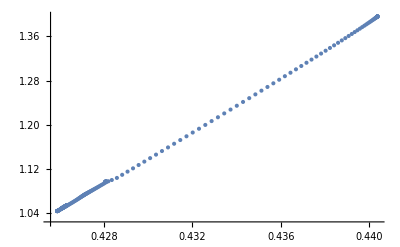

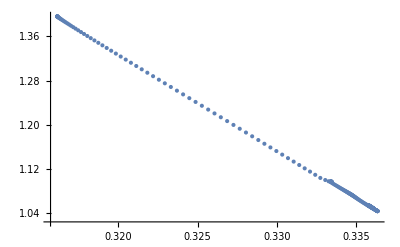

```mathematica
(*-----------------confirm perturbation response is not due to moment arms------------*)
(*inverse of the slope is moment arm for elbow muscles*)
ListPlot[Thread[{lenDATA[[;;,4]],qposDATA[[;;,2]]}]]
ListPlot[Thread[{lenDATA[[;;,3]],qposDATA[[;;,2]]}]]
```

## Unused scrap code

0.112

```mathematica
(*yrange=(*0.05*)(*0.75*)0.5;
pertTimings={
{"A03_FB_P01_f0",0.022},{"A03_FB_P02_f0",0.064},{"A03_FB_P03_f0",0.106},{"A03_FB_P04_f0",0.148},
{"A03_FB_P01_f1",0.032},{"A03_FB_P02_f1",0.094},{"A03_FB_P03_f1",0.158},{"A03_FB_P04_f1",0.222},
{"A03_FB_P01_f2",0.038},{"A03_FB_P02_f2",0.116},{"A03_FB_P03_f2",0.192},{"A03_FB_P04_f2",0.270}
};
(*perturbation never happens for controls, so make start time arbitrarily large*)
pertTimingsControl={{"A03_FB_P00_f0",10},{"A03_FB_P00_f1",10},{"A03_FB_P00_f2",10}};
pertTimings=Join[pertTimings,pertTimingsControl];
pertStart=pertTimings[[Position[pertTimings,trialname][[1,1]]]][[2]];
pertEnd=pertStart+0.018;*)
```

Note that the timing of zero crossings (particularly for elbow and wrist) don’t match exactly with net joint torque - I think this is because flex/ext have different max torques - I tried to account for this, but there may be some issues with moment arms not being constant in the simulation, however these torque values (specifically the “a” factor assumes constant max torque).  This is very off for A03_FB_P00_f2 elbow where torque values match only if a is quite low.  There must be an issue due to the increased range of motion for this target and moment arm values.

```mathematica
trialname
```

A03_FB_P00_f2

```mathematica
pertTimings
```

{{A03_FB_P01_f0,0.022},{A03_FB_P02_f0,0.064},{A03_FB_P03_f0,0.106},{A03_FB_P04_f0,0.148},{A03_FB_P01_f1,0.032},{A03_FB_P02_f1,0.094},{A03_FB_P03_f1,0.158},{A03_FB_P04_f1,0.222},{A03_FB_P01_f2,0.038},{A03_FB_P02_f2,0.116},{A03_FB_P03_f2,0.192},{A03_FB_P04_f2,0.27}}

```mathematica
dirreachingSims
```

/Users/chris/Desktop/WTageing/CODE/reaching-arm-model-CTR/outputData/setN02_ALL

```mathematica
SetDirectory[dirreachingSims]
Export[trialname<>"_SHO_2D.mov",animation];
ResetDirectory[]
```

/Users/chris/Desktop/WTageing/CODE/reaching-arm-model-CTR/outputData/setN02_ALL

/Users/chris

```mathematica
dirreachingSims
```

/Users/chrisrichards/Desktop/WTageing/DATA/reachingSims/output/setN02_ALL

```mathematica
Dynamic[status]
range=4.5;
pntsize=0.03;
animSize=500;
view1={0.15,{3,2,2},{0.5,0.25,0.5}};(*view angle, view point,view centre*)
view2={0.1,{4,0,0},{.5, 0.33, 0.5}};
view2zoom={0.02,{4,0,0},{0.2,0.5, 0.5}};
(*view2=view2zoom;*)
pntsize=If[view2==view2zoom,0.003,pntsize];
view3={0.15,{-2,2,3},{.5, 0.6, 0.85}};
view3zoom={(*0.15*)0.03,{-2,2,3},{.57, 0.7, 0.85}};
(*view3=view3zoom;*)
view=view1;
plotA=ListPlot3D[{ceilingDATA,floorDATA}(*,Filling->{1->{2}}*),PlotStyle->{{Pink,Opacity[0.7]},{Black,Opacity[0.1]}},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},Boxed->False,Axes->False];
plotB=ListPlot3D[groundplanedata,PlotStyle->{Gray,Opacity[0.1]}];

ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->Red,Axes->False,Boxed->False];


Manipulate(*animation=Table*)[
status=fr;
slice=(*fr-1*);;fr;
(*p1=Show[ListPlot3D[{ceilingDATA,floorDATA}(*,Filling->{1->{2}}*),PlotStyle->{{Pink,Opacity[0.7]},{Black,Opacity[0.1]}},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},Boxed->False,Axes->False],
ListPointPlot3D[shofvDATA[[slice]],PlotStyle->{Black}],
ListPointPlot3D[elbfvDATA[[slice]],PlotStyle->{Red}],
ListPointPlot3D[wrifvDATA[[slice]],PlotStyle->{Blue}],
ListPlot3D[groundplanedata,PlotStyle->{Gray,Opacity[0.1]}],ImageSize->animSize,ViewAngle->view1[[1]],ViewPoint->view1[[2]],ViewCenter->view1[[3]]
];*)

actVectorScaale=0.5;
actLimitDATA={shofvActLimitDATA,elbfvActLimitDATA,wrifvActLimitDATA}[[joint]];
jointDATA={shofvDATA,elbfvDATA,wrifvDATA}[[joint]];
maxActVector=actVectorScaale*Normalize[actLimitDATA[[fr]]-jointDATA[[fr]]];
curActVector=actVectorScaale*Normalize[jointDATA[[fr]]-jointDATA[[fr-1]]];

p2=Show[plotA,
Graphics3D[{Black,Sphere[shofvDATA[[slice]],pntsize]}],
Graphics3D[{Red,Sphere[elbfvDATA[[slice]],pntsize]}],
Graphics3D[{Blue,Sphere[wrifvDATA[[slice]],pntsize]}],
(*Graphics3D[{Green,Sphere[actLimitDATA[[slice]],pntsize]}],
Graphics3D[{Cyan,Thick,Line[{jointDATA[[fr]],jointDATA[[fr]]+maxActVector}]}],
Graphics3D[{Yellow,Thick,Line[{jointDATA[[fr]],jointDATA[[fr]]+curActVector}]}],*)
(*Graphics3D[{Red,Line[{shofvDATA[[fr]],shofvActLimitDATA[[fr]]}]}],*)
plotB,ImageSize->animSize,ViewAngle->view2[[1]],ViewPoint->view2[[2]],ViewCenter->view2[[3]]
];


p3=Show[plotA,
Graphics3D[{Black,Sphere[shofvDATA[[slice]],pntsize]}],
Graphics3D[{Red,Sphere[elbfvDATA[[slice]],pntsize]}],
Graphics3D[{Blue,Sphere[wrifvDATA[[slice]],pntsize]}],
(*Graphics3D[{Green,Sphere[actLimitDATA[[slice]],pntsize]}],
Graphics3D[{Cyan,Thick,Line[{jointDATA[[fr]],jointDATA[[fr]]+maxActVector}]}],
Graphics3D[{Yellow,Thick,Line[{jointDATA[[fr]],jointDATA[[fr]]+curActVector}]}],*)
plotB,ImageSize->animSize,ViewAngle->view3[[1]],ViewPoint->view3[[2]],ViewCenter->view3[[3]]
,PlotLabel->"Time "<>IntegerString[Round[fr*mjdt*1000],10,3]<>" ms",LabelStyle->{Black,FontSize->12}];

armpoints=Partition[xyzDATA[[fr]],3];
plotArm=Graphics3D[{Thickness[0.003],Line[armpoints]}];
plotC=Show[ptarget,plotArm,Box->False,ViewPoint->Top,ViewAngle->0.4,ImageSize->800];

plot=GraphicsRow[{p3,p2},ImageSize->1000(*,Inset[plotC]*)];
Overlay[{plot,plotC},Alignment->Center]

,{fr,2,Length[actDATA],1},{joint,1,3,1}]
animation[[-1]]
```

Visualization`Core`ListPlot3D::arrayerr: -- Message text not found -- ({{},{}})

Part::partd: Part specification animation⟦-1⟧ is longer than depth of object.

animation⟦-1⟧

```mathematica
p2
```

```mathematica
Manipulate[animation[[fr]],{fr,1,Length[animation],1}]
```

```mathematica
.27/mjdt
```

135.

```mathematica
ListPlot[shofvDATA[[;;,3]]]
```

```mathematica
Directory[]
```

/Users/chrisrichards

```mathematica
SetDirectory[dirreachingSims]
Export[trialname<>"_rescaled.mov",animation]
ResetDirectory[]
```

/Users/chrisrichards/Desktop/WTageing/DATA/reachingSims/output/setN02_ALL

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

A03_FB_P00_s1_rescaled.mov

/Users/chrisrichards/Desktop/WTageing/DATA/reachingSims/output/setN02_ALL

```mathematica
SetDirectory[dirreachingSims]
Export[trialname<>".png",figurePlot]
ResetDirectory[]
```

/Users/chrisrichards/Desktop/WTageing/DATA/reachingSims/output/setN02_ALL

A03_FB_P00_s0.png

/Users/chrisrichards

```mathematica
dirreachingSims
```

/Users/chrisrichards/Desktop/WTageing/DATA/reachingSims/output/setN02_ALL

## Copy of functioning joint-fv code, but before cleaning/commenting

```mathematica
Clear[shofvDATA2D,elbfvDATA2D,wrifvDATA2D]
actScale=1.;(*defunct scaling term for code development - leave = 1 always*)

(*--allocate space for fv ceiling data (ceiling is the max value on joint-fv curve for given level of activation)--*)
fvceilingSho={};
fvceilingElb={};
fvceilingWri={};

(*--allocate space for joint-fv plots for all joints---*)
shofvDATA2D={};
elbfvDATA2D={};
wrifvDATA2D={};

(*--allocate space for joint-fv data for all joints; pos means position on joint-fv curve ---*)
shofvposDATA={};
elbfvposDATA={};
wrifvposDATA={};

(*--allocate space for position data on of antagonist muscle----*)
fvantposSho={};
fvantposElb={};
fvantposWri={};

(*plot styles*)
stylesFVcurves={{Black,Dashed},(*Darker[Darker[Green]]*)Gray,{Gray,Dashed}};

flON=False;(*turn on or off FL effects*)

(*--------------------------------------*)
(*---joint-fv computations for shoulder----*)
(*--------------------------------------*)
ijoint=1;
muscleSwap=-1;(*make -1 if you want to swap agonist/antagonist*)
iMus={{1,2},{3,4},{5,6}}[[ijoint]];(*extract indices for flexor and extensor muscles*)
(*-- calculate muscle power for flexor and extensor during first 50 time samples---*)
(*--the muscle that generates most power first is the "dominant" muscle therefore defined as the agonist*)
(*this ant/ag designation will remain constant through the trial*)
meanpwrFlx=Mean[pwrDATA[[1;;50,iMus[[1]]]]];(*avg power for flexor*)
meanpwrExt=Mean[pwrDATA[[1;;50,iMus[[2]]]]];(*avg power for extensor*)
powerPoints={meanpwrFlx,meanpwrExt};
imax=Ordering[powerPoints,muscleSwap*-1][[1]];(*indicies that allow the ordering of flexor/extensor values based on their values*)
imin=Ordering[powerPoints,muscleSwap*1][[1]];
a=tmaxValues[[iMus]][[imin]]/tmaxValues[[iMus]][[imax]];(*this ratio determines how much to scale antagonist - i.e. we need to account for different muscle fmax values to weight their contributions to the joint-fv curve*)
shofvActLimitDATA={};
Do[
testtime=itr(*200*);
tmaxAg=tmaxValues[[iMus[[1]]]];(*max torque for flexor*)
tmaxAnt=tmaxValues[[iMus[[2]]]];(*max torque for extensor*)
(*a=tmaxAnt/tmaxAg;(*how much to scale antagonist*)*)
(*maxactIndex=Ordering[actDATA[[;;,iMus]],-1][[1]];*)(*4.6.2024 index when max activation reached*)
actPoints=actScale*actDATA[[testtime,iMus]];
flgPoints=flgDATA[[testtime,iMus]];
fvgPoints=fvgDATA[[testtime,iMus]];
asho=a;(*activation ratio for shoulder - for checking/debugging purposes*)
actMax=actPoints[[imax]](*Max[actPoints]*);
actMin=actPoints[[imin]](*Min[actPoints]*);
(*account for FL affects*)
flgMax=If[flON,flgPoints[[imax]],1];
flgMin=If[flON,flgPoints[[imin]],1];
fvgMax=fvgPoints[[imax]];
fvgMin=fvgPoints[[imin]];

actangle=Pi*(1-actMax);(*defunct line*)
velPoints=velDATA[[testtime,iMus]];
(*velPointsMean=Sign[velPoints]*Mean[Abs[velPoints]];(*they're not exaclty mirrored, so take average*);*)
(*velpos=Abs[velPointsMean[[1]]];*)(*vm coordinate on FV curve*)
velpos=-velPoints[[imax]]*mlps2rpsSho;(*convert X coordinate to rad/s*)
(*vm coordinate on FV curve- must be negated because shortening velocity is negative*)

(*fvceiling=flgMax*actMax*(FV/.vm->velpos)/.vm->velpos;*)
(*highest point in FV volume for that act level*)
fvceiling=flgMax*fvgMax*actMax;
fvceilingSho=Join[fvceilingSho,{fvceiling}];
(*fvantpos=flgMin*actMin*(FVant/.vm->velpos)/.vm->velpos;*)
fvantpos=flgMin*fvgMin*actMin;
(*point on lower activated muscle's FV curve*)
fvantposSho=Join[fvantposSho,{fvantpos}];
fvpos={velpos,0,fvceiling-a*fvantpos};(*joint operating point in joint FV volume*)

(*-------------------------------------------------------------------------------------------------------------*)

(*----save 2D fv plot data before making it 3D---*)
shofvposDATA=Join[shofvposDATA,{fvpos[[{1,3}]]}];
pointcol={Black,Red,Blue}[[1]];
pointsize=0.03;
jointFVsho={vm,0,FVsho};(*UNUSED*)
jointFVantsho={vm,0,FVantsho};(*UNUSED*)
jointFVscaled=jointFVsho;(*UNUSED*)
jointFVscaled[[3]]=actPoints[[imax]]*FVsho;(*top curve*)
jointFVantScaled=jointFVantsho;(*UNUSED*)
jointFVantScaled[[3]]=actPoints[[imax]]*FVsho-a*actPoints[[imin]]*FVantsho;(*middle curve*)
jointFVantScaledMax=jointFVantsho;(*UNUSED*)
jointFVantScaledMax[[3]]=actPoints[[imax]]*FVsho-a*Max[actPoints]*FVantsho;(*UNUSED bottom curve*)
jointFVantScaledMaxalt=-a*actPoints[[imin]]*FVantsho;(*bottom curve*)
plotfv2D=Show[
Plot[{jointFVscaled[[3]],jointFVantScaled[[3]],(*jointFVantScaledMax[[3]]*)jointFVantScaledMaxalt},{vm,-vmaxrpsSho,vmaxrpsSho},PlotRange->{-2*Max[actDATA],2*Max[actDATA](*-5,5*)},AspectRatio->1,PlotStyle->stylesFVcurves],
ListPlot[{shofvposDATA[[-1]]},PlotStyle->pointcol],
ListPlot[shofvposDATA,PlotStyle->{pointcol,Opacity[0.2]}]
];
shofvDATA2D=Join[shofvDATA2D,{plotfv2D}];
(*---------------------------------------------*)

(*to rotate it into the visualisation volume*)
(*fvposr=fvTransform[fvpos]*)
,{itr,1,Length[actDATA]}];

(*--------------------------------------*)
(*---joint-fv computations for elbow-------*)
(*--------------------------------------*)

ijoint=2;
muscleSwap=1;(*make -1 if you want to swap agonist/antagonist*)
iMus={{1,2},{3,4},{5,6}}[[ijoint]];
meanpwrFlx=Mean[pwrDATA[[1;;50,iMus[[1]]]]];
meanpwrExt=Mean[pwrDATA[[1;;50,iMus[[2]]]]];
powerPoints={meanpwrFlx,meanpwrExt};
imax=Ordering[powerPoints,muscleSwap*-1][[1]];
imin=Ordering[powerPoints,muscleSwap*1][[1]];
a=tmaxValues[[iMus]][[imin]]/tmaxValues[[iMus]][[imax]];(*how much to scale antagonist*)

elbfvActLimitDATA={};
Do[
testtime=itr(*200*);
tmaxAg=tmaxValues[[iMus[[1]]]];(*max torque for flexor*)
tmaxAnt=tmaxValues[[iMus[[2]]]];(*max torque for extensor*)
(*a=tmaxAnt/tmaxAg;*)(*how much to scale antagonist*)
(*maxactIndex=Ordering[actDATA[[;;,iMus]],-1][[1]];*)(*4.6.2024 index when max activation reached*)
actPoints=actScale*actDATA[[testtime,iMus]];
flgPoints=flgDATA[[testtime,iMus]];
fvgPoints=fvgDATA[[testtime,iMus]];

aElb=a;(*activation ratio for elbow*)

actMax=actPoints[[imax]](*Max[actPoints]*);
actMin=actPoints[[imin]](*Min[actPoints]*);
(*account for FL affects*)
flgMax=If[flON,flgPoints[[imax]],1];
flgMin=If[flON,flgPoints[[imin]],1];
fvgMax=fvgPoints[[imax]];
fvgMin=fvgPoints[[imin]];

actangle=Pi*(1-actMax);
velPoints=velDATA[[testtime,iMus]];
(*velPointsMean=Sign[velPoints]*Mean[Abs[velPoints]];(*they're not exaclty mirrored, so take average*);*)
(*velpos=Abs[velPointsMean[[1]]];*)(*vm coordinate on FV curve*)
velpos=-velPoints[[imax]]*mlps2rpsElb;
(*velpos=-Sign[velPoints[[imax]]]*Mean[Abs[velPoints]]*mlps2rpsElb;*)(*average because moment arms are different*)
(*velpos=Sign[velPoints[[imax]]]*qvelDATAsec[[testtime,ijoint,2]];*)(*joint velocity*)
(*vm coordinate on FV curve- must be negated because shortening velocity is negative*)

(*fvceiling=flgMax*actMax*(FV/.vm->velpos)/.vm->velpos;*)
(*highest point in FV volume for that act level*)
fvceiling=flgMax*fvgMax*actMax;
fvceilingElb=Join[fvceilingElb,{fvceiling}];
(*fvantpos=flgMin*actMin*(FVant/.vm->velpos)/.vm->velpos;*)
fvantpos=flgMin*fvgMin*actMin;
(*point on lower activated muscle's FV curve*)
fvantposElb=Join[fvantposElb,{fvantpos}];
fvpos={velpos,0,fvceiling-a*fvantpos};(*joint operating point in joint FV volume*)
(*fvTransform=RotationTransform[actangle,{0,0,1},anchor];*)


(*-------------------------------------------------------------------------------------------------------------*)

(*----save 2D fv plot data before making it 3D---*)
elbfvposDATA=Join[elbfvposDATA,{fvpos[[{1,3}]]}];
pointcol={Black,Red,Blue}[[1]];
pointsize=0.03;
jointFVelb={vm,0,FVelb};
jointFVantelb={vm,0,FVantelb};
jointFVscaled=jointFVelb;
jointFVscaled[[3]]=actPoints[[imax]]*FVelb;
jointFVantScaled=jointFVantelb;
jointFVantScaled[[3]]=actPoints[[imax]]*FVelb-a*actPoints[[imin]]*FVantelb;
jointFVantScaledMax=jointFVantelb;
jointFVantScaledMax[[3]]=actPoints[[imax]]*FVelb-a*Max[actPoints]*FVantelb;
jointFVantScaledMaxalt=-a*actPoints[[imin]]*FVantelb;
plotfv2D=Show[
Plot[{jointFVscaled[[3]],jointFVantScaled[[3]],(*jointFVantScaledMax[[3]]*)jointFVantScaledMaxalt},{vm,-vmaxrpsElb,vmaxrpsElb},PlotRange->{-2*Max[actDATA],2*Max[actDATA](*-5,5*)},AspectRatio->1,PlotStyle->stylesFVcurves],
ListPlot[{elbfvposDATA[[-1]]},PlotStyle->pointcol],
ListPlot[elbfvposDATA,PlotStyle->{pointcol,Opacity[0.2]}]
];
elbfvDATA2D=Join[elbfvDATA2D,{plotfv2D}];
(*---------------------------------------------*)

(*to rotate it into the visualisation volume*)
(*fvposr=fvTransform[fvpos]*)
,{itr,1,Length[actDATA]}];


(*--------------------------------------*)
(*---joint-fv computations for wrist-------*)
(*--------------------------------------*)

ijoint=3;
muscleSwap=1;(*make -1 if you want to swap agonist/antagonist*)
iMus={{1,2},{3,4},{5,6}}[[ijoint]];
meanpwrFlx=Mean[pwrDATA[[1;;50,iMus[[1]]]]];
meanpwrExt=Mean[pwrDATA[[1;;50,iMus[[2]]]]];
powerPoints={meanpwrFlx,meanpwrExt};
imax=Ordering[powerPoints,muscleSwap*-1][[1]];
imin=Ordering[powerPoints,muscleSwap*1][[1]];
a=tmaxValues[[iMus]][[imin]]/tmaxValues[[iMus]][[imax]];(*how much to scale antagonist*)

wrifvActLimitDATA={};
Do[
testtime=itr(*200*);
tmaxAg=tmaxValues[[iMus[[1]]]];(*max torque for flexor*)
tmaxAnt=tmaxValues[[iMus[[2]]]];(*max torque for extensor*)
(*a=tmaxAnt/tmaxAg;(*how much to scale antagonist*)*)
(*maxactIndex=Ordering[actDATA[[;;,iMus]],-1][[1]];*)(*4.6.2024 index when max activation reached*)
actPoints =actScale*actDATA[[testtime,iMus]];
flgPoints=flgDATA[[testtime,iMus]];
fvgPoints=fvgDATA[[testtime,iMus]];

(*rather than defining agonist/antagonist based on activation, do it based on producing positive power*)
(*take first chunk of data, see which muscle is producing positive power*)
(*this ant/ag designation will remain constant through the trial*)

awri=a;(*activation ratio for wrist*)
actMax=actPoints[[imax]](*Max[actPoints]*);
actMin=actPoints[[imin]](*Min[actPoints]*);
(*account for FL affects*)
flgMax=If[flON,flgPoints[[imax]],1];
flgMin=If[flON,flgPoints[[imin]],1];
fvgMax=fvgPoints[[imax]];
fvgMin=fvgPoints[[imin]];

actangle=Pi*(1-actMax);
velPoints=velDATA[[testtime,iMus]];
(*velPointsMean=Sign[velPoints]*Mean[Abs[velPoints]];(*they're not exaclty mirrored, so take average*);*)
(*velpos=Abs[velPointsMean[[1]]];*)(*vm coordinate on FV curve*)
velpos=-velPoints[[imax]]*mlps2rpsWri;(*vm coordinate on FV curve- must be negated because shortening velocity is negative*)

(*fvceiling=flgMax*actMax*(FV/.vm->velpos)/.vm->velpos;*)
(*highest point in FV volume for that act level*)
fvceiling=flgMin*fvgMax*actMax;
fvceilingWri=Join[fvceilingWri,{fvceiling}];
(*fvantpos=flgMin*actMin*(FVant/.vm->velpos)/.vm->velpos;*)
fvantpos=flgMin*fvgMin*actMin;
(*point on lower activated muscle's FV curve*)
fvantposWri=Join[fvantposWri,{fvantpos}];
fvpos={velpos,0,fvceiling-a*fvantpos};(*joint operating point in joint FV volume*)
(*fvTransform=RotationTransform[actangle,{0,0,1},anchor];*)

(*-------------------------------------------------------------------------------------------------------------*)

(*----save 2D fv plot data before making it 3D---*)
wrifvposDATA=Join[wrifvposDATA,{fvpos[[{1,3}]]}];
pointcol={Black,Red,Blue}[[1]];
pointsize=0.03;
jointFVwri={vm,0,FVwri};
jointFVantwri={vm,0,FVantwri};
jointFVscaled=jointFVwri;
jointFVscaled[[3]]=actPoints[[imax]]*FVwri;
jointFVantScaled=jointFVantwri;
jointFVantScaled[[3]]=actPoints[[imax]]*FVwri-a*actPoints[[imin]]*FVantwri;
jointFVantScaledMax=jointFVantwri;
jointFVantScaledMax[[3]]=actPoints[[imax]]*FVwri-a*Max[actPoints]*FVantwri;
jointFVantScaledMaxalt=-a*actPoints[[imin]]*FVantwri;
plotfv2D=Show[
Plot[{jointFVscaled[[3]],jointFVantScaled[[3]],(*jointFVantScaledMax[[3]]*)jointFVantScaledMaxalt},{vm,-vmaxrpsWri,vmaxrpsWri},PlotRange->{-2*Max[actDATA],2*Max[actDATA](*-5,5*)},AspectRatio->1,PlotStyle->stylesFVcurves],
ListPlot[{wrifvposDATA[[-1]]},PlotStyle->pointcol],
ListPlot[wrifvposDATA,PlotStyle->{pointcol,Opacity[0.2]}]
];
wrifvDATA2D=Join[wrifvDATA2D,{plotfv2D}];
(*---------------------------------------------*)

(*to rotate it into the visualisation volume*)
(*fvposr=fvTransform[fvpos]*)
,{itr,1,Length[actDATA]}];

yrange=(*0.05*)(*0.75*)0.5;
(*timings of the perturbation - absolute times vary because the have been triggered in relative times*)
pertTimings={
{"A03_FB_P01_f0",0.022},{"A03_FB_P02_f0",0.064},{"A03_FB_P03_f0",0.106},{"A03_FB_P04_f0",0.148},
{"A03_FB_P01_f1",0.032},{"A03_FB_P02_f1",0.094},{"A03_FB_P03_f1",0.158},{"A03_FB_P04_f1",0.222},
{"A03_FB_P01_f2",0.038},{"A03_FB_P02_f2",0.116},{"A03_FB_P03_f2",0.192},{"A03_FB_P04_f2",0.270}
};
(*perturbation never happens for controls, so make start time arbitrarily large*)
pertTimingsControl={{"A03_FB_P00_f0",10},{"A03_FB_P00_f1",10},{"A03_FB_P00_f2",10}};
pertTimings=Join[pertTimings,pertTimingsControl];
pertStart=pertTimings[[Position[pertTimings,trialname][[1,1]]]][[2]];
pertEnd=pertStart+0.018;
```

```mathematica
(*------------------------------------------------------*)
(*---interactive cell for animating joint fv trajectories---*)
(*------------------------------------------------------*)
range=1;
ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->Red,Axes->False,Boxed->False];
(*reachAnim=Table*)

joint=1;(*1=sho; 2=elb; 3=wri*)
(*animation=Table*)Manipulate[
time=ToString[NumberForm[fr*mjdt,{3,3}]]<>"s";
labelnormal=Style[time,Black,Bold,20];
labelperturb=Style[time,Red,Bold,20];
label=If[pertStart<=fr*mjdt<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->label];
GraphicsRow[{plot1,plot2},ImageSize->800]


,{fr,1,Length[shofvDATA2D],1},{joint,1,3,1}]
```

```mathematica
(*------------------------------*)
(*---export the jointfv data----*)
(*------------------------------*)
SetDirectory[dirMSdata];(*as defined in ReachingLimitsFigures.nb*)
Export["shofvposDATA_"<>trialname<>".csv",shofvposDATA]
Export["elbfvposDATA_"<>trialname<>".csv",elbfvposDATA]
Export["wrifvposDATA_"<>trialname<>".csv",wrifvposDATA]
ResetDirectory[];
```

shofvposDATA_A03_FB_P00_f2.csv

elbfvposDATA_A03_FB_P00_f2.csv

wrifvposDATA_A03_FB_P00_f2.csv

```mathematica
(*---------------------------------------------*)
(*---------------------------------------------*)
(*---------------------------------------------*)
(*---------------------------------------------*)
(*-----ANALYSE COMPONENTS OF dTORQUE/dt--------*)
(*---------------------------------------------*)
(*----note: much of this is exploratory and-----*)
(*-----hypothetical, but some parameters are----*)
(*-----needed to generate the figure about------*)
(*------torque rates and activation rates-------*)
(*---------------------------------------------*)
```

```mathematica
jntindex=2;(*1 = sho; 2 = elbow; 3 = wrist*)
prange={-6,10};(*y value range for plotting*)
flexOrExt=0;(*0 for flex 1 for ext*)
index=(jntindex-1)+jntindex+flexOrExt;(*index of the relevant muscle*)

(*activation data for Flx, Ext*)
adataFlx=actDATA[[;;,index]];
adataExt=actDATA[[;;,index+1]];

(*flg data for Flx, Ext*)
flgFlx=flgDATA[[;;,index]];
flgExt=flgDATA[[;;,index+1]];

(*fvg data for Flx, Ext*)
fvgFlx=fvgDATA[[;;,index]];
fvgExt=fvgDATA[[;;,index+1]];

(*muscle vel data for Flx, Ext*)
vdataFlx=velDATA[[;;,index]];
vdataExt=velDATA[[;;,index+1]];

(*moment arm data for Flx, Ext*)
rflx=rValues[[index]];
rext=rValues[[index+1]];

(*derivatives of the above*)
dadataFlx=1*Differentiator1D[adataFlx,mjdt];
dadataExt=1*Differentiator1D[adataExt,mjdt];

dflgFlx=1*Differentiator1D[flgFlx,mjdt];
dflgExt=1*Differentiator1D[flgExt,mjdt];

dfvgFlx=1*Differentiator1D[fvgFlx,mjdt];
dfvgExt=1*Differentiator1D[fvgExt,mjdt];

(*-----------------------------------------------------------------------------*)
(*mostly unused calculations for curiosity, pending further analysis and checking*)
(*-----------------------------------------------------------------------------*)
tqmax=tmaxValues[[jntindex]];
fmaxFlx=fmaxValues[[index]];
fmaxExt=fmaxValues[[index+1]];
(*c=qfrcDATA[[;;,jntindex]];*)
fdataFlx=frcDATA[[;;,index]];
fdataExt=frcDATA[[;;,index+1]];
dfdataFlx=Differentiator1D[fdataFlx,mjdt];
dfdataExt=Differentiator1D[fdataExt,mjdt];

dfdataFlxCal=flgFlx*fvgFlx*dadataFlx+adataFlx*fvgFlx*dflgFlx+adataFlx*flgFlx*dfvgFlx;
dfdataExtCal=flgExt*fvgExt*dadataExt+adataExt*fvgExt*dflgExt+adataExt*flgExt*dfvgExt;

ddataFlxCalnofvg=1*1*dadataFlx+adataFlx*fvgFlx*0+adataFlx*flgFlx*0;
ddataExtCalnofvg=1*1*dadataExt+adataExt*fvgExt*0+adataExt*flgExt*0;

ddataFlxCalnoact=flgFlx*fvgFlx*dadataFlx*0+adataFlx*fvgFlx*dflgFlx*0+adataFlx*flgFlx*dfvgFlx;
ddataExtCalnoact=flgExt*fvgExt*dadataExt*0+adataExt*fvgExt*dflgExt*0+adataExt*flgExt*dfvgExt;

dtorqueCal=fmaxFlx*rflx*dfdataFlxCal-fmaxExt*rext*dfdataExtCal;
Print["dtorque Limits"]
Print["positive dtorque limits: flexor, extensor"]
dtorqueLimitPos={fmaxFlx*rflx*maxActRate,fmaxExt*rext*maxActRate}
Print["negative dtorque limit"]
dtorqueLimitNeg={fmaxFlx*rflx*maxDeactRate-fmaxExt*rext*maxActRate,fmaxExt*rext*maxDeactRate-fmaxFlx*rflx*maxActRate}
dtorqueCaloFVGflx=fmaxFlx*rflx*ddataFlxCalnofvg;
dtorqueCaloFVGext=fmaxExt*rext*ddataExtCalnofvg;
dtorqueCalNoFVG=dtorqueCaloFVGflx-dtorqueCaloFVGext;
dtorqueFVGflx=fmaxFlx*rflx*dfvgFlx;
dtorqueFVGext=fmaxExt*rext*dfvgExt;
dtorqueCalFVG=dtorqueFVGflx+dtorqueFVGext;
dtorqueCalNoACT=fmaxFlx*rflx*ddataFlxCalnoact-fmaxExt*rext*ddataExtCalnoact;
tdata=qfrcDATA[[;;,jntindex]];

dtorque=Differentiator1D[tdata,mjdt];

torqueXY=Thread[{timeData,tdata}];
dtorqueXY=Thread[{timeData,dtorque}];
dtorqueCalXY=Thread[{timeData,dtorqueCal}];
dtorqueCalNoFVGXY=Thread[{timeData,dtorqueCalNoFVG}];
dtorqueCalNoACTXY=Thread[{timeData,dtorqueCalNoACT}];

(*-----------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------*)
(*-----------------------------------------------------------------------------*)

(*create unformatted plots for inspection - these figures are for curiosity not publication*)
(*further mathematical analysis/confirmation is needed*)

Show[
p1=ListLinePlot[{dtorqueXY,dtorqueCalXY,dtorqueCalNoFVGXY,dtorqueCalNoACTXY},PlotStyle->{Black,Gray,Red,{Blue,Dashed}},PlotRange->{Automatic,{-3000,2000}},PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]],
p1a=ListLinePlot[{{0,dtorqueLimitPos[[1]]},{cutoff,dtorqueLimitPos[[1]]}},PlotStyle->{Black,Dashed}],
p1b=ListLinePlot[{{0,dtorqueLimitPos[[2]]},{cutoff,dtorqueLimitPos[[2]]}},PlotStyle->{Black,Dashed}]
]
ListPlot[{fdataFlx*rflx-fdataExt*rext,tdata},Joined->{False,True}]
ListPlot[{dfdataFlx,fmaxFlx*dfdataFlxCal,fmaxFlx*ddataFlxCalnofvg},PlotStyle->{Black,Red,Blue},PlotRange->All,PlotLabel->"d force"]
ListLinePlot[{dtorque,dtorqueFVGflx,dtorqueFVGext,dtorqueCalFVG},PlotRange->All,PlotLabel->{"dtorque","dtorquefvgFlx","dtorquefvgExt","total"},PlotStyle->{Black,Red,Blue,Purple}]
ListLinePlot[{rflx*fmaxFlx*ddataFlxCalnofvg-rext*fmaxExt*ddataExtCalnofvg,rflx*fmaxFlx*ddataFlxCalnofvg,-rflx*fmaxFlx*ddataExtCalnofvg},PlotStyle->{Black,Red,Blue},PlotLabel->{"net torque noFVG","flexor noFVG","extensor, noFVG"}]

ListLinePlot[{dtorque,fmaxFlx*rflx*ddataFlxCalnoact,fmaxExt*rext*ddataExtCalnoact,dtorqueCalNoACT},PlotStyle->{Black,Red,Blue,Purple},PlotRange->All]

p2=ListLinePlot[qfrcDATAsec[[;;,jntindex]],PlotStyle->{colors3[[jntindex]]},PlotRange->{Automatic,{-18,18}},PlotStyle->styles3,BaseStyle->graphstyle,ImageSize->size,AxesStyle->Thickness[axthickness]];

GraphicsColumn[{p2,Show[p1,p1a,p1b]}]
```

3

dtorque Limits

positive dtorque limits: flexor, extensor

{493.558,379.66}

negative dtorque limit

{-726.643,-760.468}

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

Perturbation timings
target 0
1: 0.022-0.04
2: 0.064-0.082
3: 0.106-0.124
4: 0.148-0.166

target 1
1: 0.032-0.05
2: 0.094-0.112
3: 0.158-0.176
4: 0.222-0.240

target 2
1: 0.038-0.056
2: 0.116-0.134
3: 0.192-0.210
4: 0.270-0.288

```mathematica
(*-----------------confirm perturbation response is not due to moment arms------------*)
(*inverse of the slope is moment arm for elbow muscles*)
ListPlot[Thread[{lenDATA[[;;,4]],qposDATA[[;;,2]]}]]
ListPlot[Thread[{lenDATA[[;;,3]],qposDATA[[;;,2]]}]]
```

-Graphics-

-Graphics-

```mathematica
(*additionally, moment arm of elbow flexor was too low - other ones seem to be fine*)
```

```mathematica
ijoint=2;
iMus={{1,2},{3,4},{5,6}}[[ijoint]];
dataFlx=Thread[{qvelDATA[[;;,2]],velDATAmps[[;;,iMus[[1]]]]}];
dataExt=Thread[{qvelDATA[[;;,2]],velDATAmps[[;;,iMus[[2]]]]}];
ListPlot[dataFlx]
ListPlot[dataExt]
LinearModelFit[dataFlx,x,x]
LinearModelFit[dataExt,x,x]
```

## OLD/UNUSED CODE Compare among conditions

```mathematica
trialnameList=(*{"A03_FB_P00_f0","A03_FB_P04_f0"}*)(*{"A03_FB_P00_f1","A03_FB_P03_f1"}*){"A03_FB_P00_f1","A03_FB_P01_f1","A03_FB_P02_f1","A03_FB_P04_f1"};(* "A03_FB_P02_f1"  or -1 for most recent run, saved in the root of the mujoco folder*)
timeDDATA={};
actDDATA={};
ctrqDDATA={};
fvgDDATA={};
flgDDATA={};
Do[
trialname=trialnameList[[itr]];
prefix=trialname<>"_";
trialnum=ToExpression[StringTake[trialname,-1]]+1;(*the reach target index*)
(*trialnum="1";
mostRecentQ=trialname==-1;*)
(*dirtrial=dirdata<>trialname<>"/";
dirtrial=If[mostRecentQ,dirmodel,dirtrial];*)
SetDirectory[dirreachingSims];
(*extract cutoff index from metadata file*)

(*If[!mostRecentQ,
trialrow=(Position[metadata[[;;,1]],trialname]//Flatten)[[1]]+ToExpression[trialnum];
cutoff=metadata[[trialrow,4]];
,
cutoff=-1
];*)
cutoffFile=prefix<>"cutoffData.csv";
cutoffData=Import[cutoffFile,"Data"];
cutoff=If[Length[Flatten[cutoffData]]==0,-1,cutoffData[[1,1]]];

(*cutoff=400;*)(*for control condition - reach 0*)
(*cutoff=620;(*for control condition - reach 1*)*)
slice=1;;cutoff;
(*slice=190;;350;*)

(*targetfile="targ_setN01.txt";
str=Import[targetfile,"Text"];
targets=ImportString[str,"Table","FieldSeparators"->{";"}][[;;,{1,2}]];
targetXYZ=targets[[ToExpression[trialnum]+1]];
targetXYZ=Join[targetXYZ,{0}];*)
targetXYZ=targets[[trialnum]];
colors={Black,Black,Red,Red,Blue,Blue};
colors3={Black,Red,Blue};(*for plots with 3 lines instead of 6*)
plotthickness=0.007;
(*dashings={Thick,Dashed,Thick,Dashed,Thick,Dashed};*)
dashings={Thickness[plotthickness],{Dashed,Thickness[plotthickness]},Thickness[plotthickness],{Dashed,Thickness[plotthickness]},Thickness[plotthickness],{Dashed,Thickness[plotthickness]}};
dashings3={Thickness[plotthickness],Thickness[plotthickness],Thickness[plotthickness]};
styles=Thread[{colors,dashings}];
styles3=Thread[{colors3,dashings3}];

xyzFile=prefix<>"xyzOutput"<>".csv";
xyzDATA=Import[xyzFile,"Data"];

errorData=Table[EuclideanDistance[Partition[xyzDATA[[i]],3][[-1]],targetXYZ],{i,1,Length[xyzDATA]}];
(*lastIndex=Flatten[Position[Threshold[errorData,0.0001],0.]][[1]];*)

mjdt=0.002;
lenFile=prefix<>"lenOutput"<>".csv";
frcFile=prefix<>"frcOutput"<>".csv";
actFile=prefix<>"actOutput"<>".csv";
fvgFile=prefix<>"fvgOutput"<>".csv";
flgFile=prefix<>"flgOutput"<>".csv";
massFile=prefix<>"massOutput"<>".csv";
qposFile=prefix<>"qposOutput"<>".csv";
qfrcFile=prefix<>"qfrcOutput"<>".csv";
ctrlFile=prefix<>"ctrlOutput"<>".csv";
ctrqFile=prefix<>"ctrqOutput"<>".csv";

lenDATA=Import[lenFile,"Data"][[slice]];
frcDATA=-Import[frcFile,"Data"][[slice]];
actDATA=Import[actFile,"Data"][[slice]];
fvgDATA=Import[fvgFile,"Data"][[slice]];
flgDATA=Import[flgFile,"Data"][[slice]];
massDATA=Import[massFile,"Data"][[slice]];
qposDATA=Import[qposFile,"Data"][[slice]];
qfrcDATA=Import[qfrcFile,"Data"][[slice]];
ctrlDATA=Import[ctrlFile,"Data"][[slice]];
ctrqDATA=Import[ctrqFile,"Data"][[slice]];

timeData=Table[i*mjdt,{i,1,Length[lenDATA]}];

timeDDATA=Join[timeDDATA,{timeData}];
actDDATA=Join[actDDATA,{actDATA}];
ctrqDDATA=Join[ctrqDDATA,{ctrqDATA}];
fvgDDATA=Join[fvgDDATA,{fvgDATA}];
flgDDATA=Join[flgDDATA,{flgDATA}];
(*DDATA=Join[DDATA,{actDATA}];*)
(*Print[ListPlot[actDATA[[;;,2]]]]*)
,{itr,1,Length[trialnameList]}]

Dimensions[DDATA2]
```

{}

```mathematica
Clear[DDATA,DDATA0,DDATA1,DDATA2,DDATA3]
```

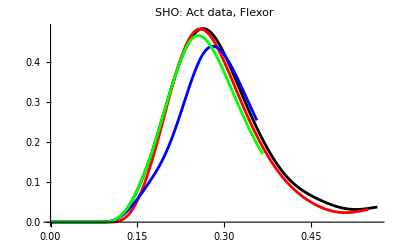

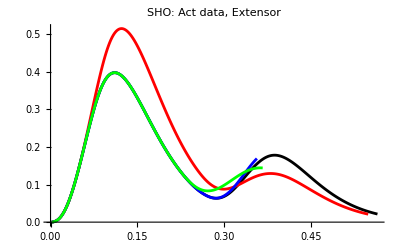

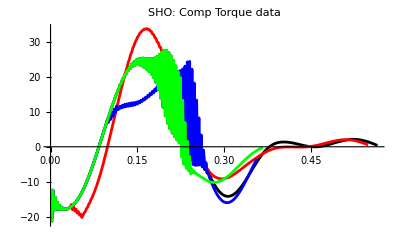

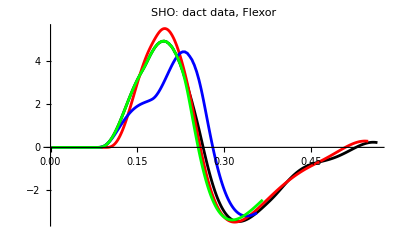

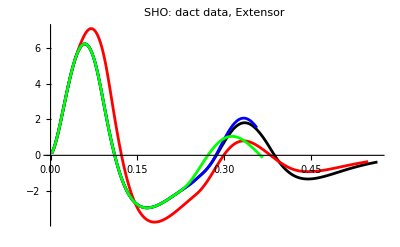

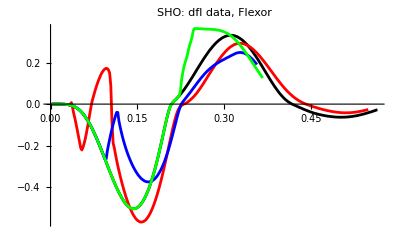

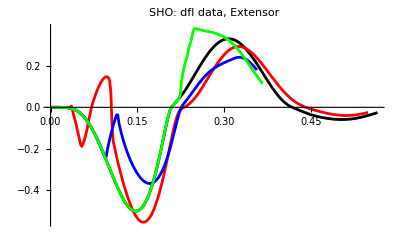

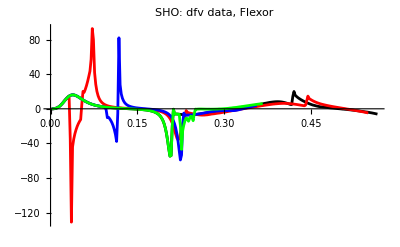

```mathematica
ijoint=1;
iMus={{1,2},{3,4},{5,6}}[[ijoint]];
actCompFlx=Table[Thread[{timeDDATA[[i]],actDDATA[[i,;;,iMus[[1]]]]}],{i,1,Length[timeDDATA]}];
actCompExt=Table[Thread[{timeDDATA[[i]],actDDATA[[i,;;,iMus[[2]]]]}],{i,1,Length[timeDDATA]}];
ctrqComp=Table[Thread[{timeDDATA[[i]],ctrqDDATA[[i,;;,ijoint]]}],{i,1,Length[timeDDATA]}];


dactCompFlx=Table[
actdata=actDDATA[[i,;;,iMus[[1]]]];
dactdata=Differentiator1D[actdata,mjdt];
Thread[{timeDDATA[[i]],dactdata}]
,{i,1,Length[timeDDATA]}];

dactCompExt=Table[
actdata=actDDATA[[i,;;,iMus[[2]]]];
dactdata=Differentiator1D[actdata,mjdt];
Thread[{timeDDATA[[i]],dactdata}]
,{i,1,Length[timeDDATA]}];

dflgCompFlx=Table[
flgdata=flgDDATA[[i,;;,iMus[[1]]]];
dflgdata=Differentiator1D[flgdata,mjdt];
Thread[{timeDDATA[[i]],dflgdata}]
,{i,1,Length[timeDDATA]}];

dflgCompExt=Table[
flgdata=flgDDATA[[i,;;,iMus[[2]]]];
dflgdata=Differentiator1D[flgdata,mjdt];
Thread[{timeDDATA[[i]],dflgdata}]
,{i,1,Length[timeDDATA]}];

dfvgCompFlx=Table[
fvgdata=fvgDDATA[[i,;;,iMus[[1]]]];
dfvgdata=Differentiator1D[fvgdata,mjdt];
Thread[{timeDDATA[[i]],dfvgdata}]
,{i,1,Length[timeDDATA]}];

dfvgCompExt=Table[
fvgdata=fvgDDATA[[i,;;,iMus[[2]]]];
dfvgdata=Differentiator1D[fvgdata,mjdt];
Thread[{timeDDATA[[i]],dfvgdata}]
,{i,1,Length[timeDDATA]}];

(*dflgExt=1*Differentiator1D[flgExt,mjdt];

dfvgFlx=1*Differentiator1D[fvgFlx,mjdt];
dfvgExt=1*Differentiator1D[fvgExt,mjdt];*)

colors={Black,Red,Blue,Green};
jointstring={"SHO: ","ELB: ","WRI: "}[[ijoint]];

ListLinePlot[actCompFlx,PlotStyle->colors,PlotLabel->jointstring<>"Act data, Flexor"]
ListLinePlot[actCompExt,PlotStyle->colors,PlotLabel->jointstring<>"Act data, Extensor"]
ListLinePlot[ctrqComp,PlotStyle->colors,PlotRange->All,PlotLabel->jointstring<>"Comp Torque data"]
ListLinePlot[dactCompFlx,PlotStyle->colors,PlotRange->All,PlotLabel->jointstring<>"dact data, Flexor"]
ListLinePlot[dactCompExt,PlotStyle->colors,PlotRange->All,PlotLabel->jointstring<>"dact data, Extensor"]
ListLinePlot[dflgCompFlx,PlotStyle->colors,PlotRange->All,PlotLabel->jointstring<>"dfl data, Flexor"]
ListLinePlot[dflgCompExt,PlotStyle->colors,PlotRange->All,PlotLabel->jointstring<>"dfl data, Extensor"]
ListLinePlot[dfvgCompFlx,PlotStyle->colors,PlotRange->All,PlotLabel->jointstring<>"dfv data, Flexor"]
ListLinePlot[dfvgCompExt,PlotStyle->colors,PlotRange->All,PlotLabel->jointstring<>"dfv data, Extensor"]
```

```mathematica
lenFile
```

A03_FB_P00_s1_lenOutput.csv

condition 1 Black, 2 Red; flexor solid; extensor dashed

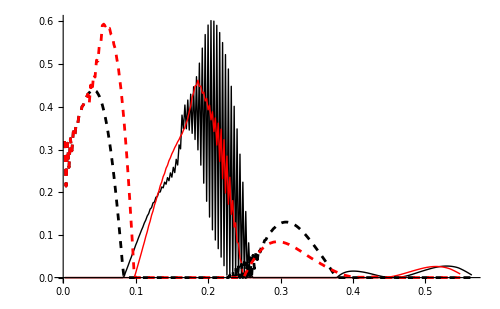

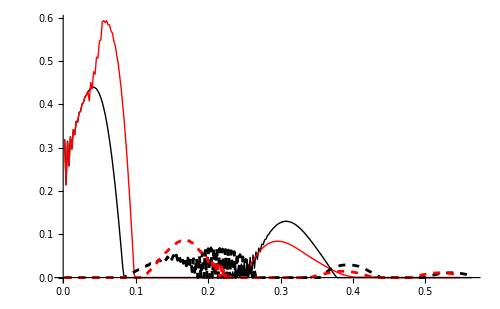

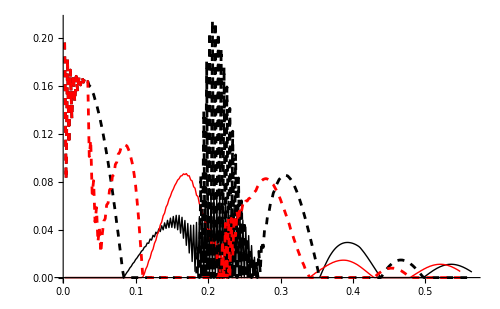

```mathematica
actDATA1=DDATA[[1]];
actDATA2=DDATA[[2]];
timeData1=Table[i*mjdt,{i,1,Length[actDATA1]}];
timeData2=Table[i*mjdt,{i,1,Length[actDATA2]}];
Print["condition 1 Black, 2 Red; flexor solid; extensor dashed"]
jointindex=1;
DATAXY1f=Thread[{timeData1,actDATA1[[;;,jointindex]]}];
DATAXY1e=Thread[{timeData1,actDATA1[[;;,jointindex+1]]}];
DATAXY2f=Thread[{timeData2,actDATA2[[;;,jointindex]]}];
DATAXY2e=Thread[{timeData2,actDATA2[[;;,jointindex+1]]}];
ListLinePlot[{DATAXY1f,DATAXY2f,DATAXY1e,DATAXY2e},PlotStyle->{{Black,Thick},{Red,Thick},{Black,Dashed},{Red,Dashed}},PlotRange->All,BaseStyle->graphstyle,ImageSize->500]
jointindex=2;
DATAXY1f=Thread[{timeData1,actDATA1[[;;,jointindex]]}];
DATAXY1e=Thread[{timeData1,actDATA1[[;;,jointindex+1]]}];
DATAXY2f=Thread[{timeData2,actDATA2[[;;,jointindex]]}];
DATAXY2e=Thread[{timeData2,actDATA2[[;;,jointindex+1]]}];
ListLinePlot[{DATAXY1f,DATAXY2f,DATAXY1e,DATAXY2e},PlotStyle->{{Black,Thick},{Red,Thick},{Black,Dashed},{Red,Dashed}},PlotRange->All,BaseStyle->graphstyle,ImageSize->500]
jointindex=3;
DATAXY1f=Thread[{timeData1,actDATA1[[;;,jointindex]]}];
DATAXY1e=Thread[{timeData1,actDATA1[[;;,jointindex+1]]}];
DATAXY2f=Thread[{timeData2,actDATA2[[;;,jointindex]]}];
DATAXY2e=Thread[{timeData2,actDATA2[[;;,jointindex+1]]}];
ListLinePlot[{DATAXY1f,DATAXY2f,DATAXY1e,DATAXY2e},PlotStyle->{{Black,Thick},{Red,Thick},{Black,Dashed},{Red,Dashed}},PlotRange->All,BaseStyle->graphstyle,ImageSize->500]
```

## OLD/UNUSED CODE (10.6.24) Joint FV volume

I’ve decided it’s OK to keep everything in terms of f/fmax and absolute velocities because we’re just looking at positions on FV curve.
The difference in agonist/antagonist torques is now accounted for in the “a” factor (April, 2024).  NOTE -  though, this means that floor will be too deep if agonist is stronger than antagonist - this affects 3D plots only for now - I’ve accounted for it in 2D plots

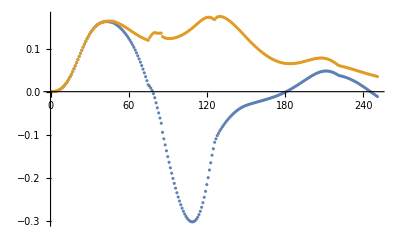

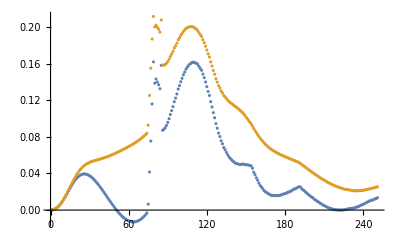

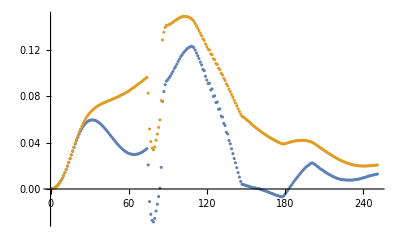

```mathematica
Clear[shofvDATA2D,elbfvDATA2D,wrifvDATA2D]
(*create ceiling of the joint FV curve*)
anchor={1.6,0,1};(*anchor point for rotation*)
actScale=1.;(*Limit to how far around activation goes around semicircle - default 1*)
jointFV={vm,0,FV};
jointFVant={vm,0,FVant};
ceilingDATA=(*Table[jointFV,{vm,-1.6,1.6,0.1}]*){};
floorDATA={};
n=10;(*number of curves*)
Do[
inc=itr/n;
scale=(1-inc);
a=1;(*how much to scale antagonist*)
fvTransform=RotationTransform[inc*Pi,{0,0,1},anchor];
jointFVscaled=jointFV;
jointFVscaled[[3]]=scale*FV;
jointFVfun=fvTransform[jointFVscaled];
data=Table[jointFVfun,{vm,-1.6,1.6,0.1}];
ceilingDATA=Join[ceilingDATA,data];
(*compute floor of volume*)
jointFVantScaled=jointFVant;
jointFVantScaled[[3]]=scale*FV-a*scale*FVant;
datafloor=Table[fvTransform[jointFVantScaled],{vm,-1.6,1.6,0.1}];
floorDATA=Join[floorDATA,datafloor];

,{itr,0,n}]

ceilingDATApartitioned=Table[
inc=itr/n;
scale=(1-inc);
a=1;(*how much to scale antagonist*)
fvTransform=RotationTransform[inc*Pi,{0,0,1},anchor];
jointFVscaled=jointFV;
jointFVscaled[[3]]=scale*FV;
jointFVfun=fvTransform[jointFVscaled];
data=Table[jointFVfun,{vm,-1.6,1.6,0.1}];
ceilingDATA=Join[ceilingDATA,data];
(*compute floor of volume*)
jointFVantScaled=jointFVant;
jointFVantScaled[[3]]=scale*FV-a*scale*FVant;
datafloor=Table[fvTransform[jointFVantScaled],{vm,-1.6,1.6,0.1}];
floorDATA=Join[floorDATA,datafloor];
data
,{itr,0,n}];
floorDATApartitioned=Table[
inc=itr/n;
scale=(1-inc);
a=1;(*how much to scale antagonist*)
fvTransform=RotationTransform[inc*Pi,{0,0,1},anchor];
jointFVscaled=jointFV;
jointFVscaled[[3]]=scale*FV;
jointFVfun=fvTransform[jointFVscaled];
data=Table[jointFVfun,{vm,-1.6,1.6,0.1}];
ceilingDATA=Join[ceilingDATA,data];
(*compute floor of volume*)
jointFVantScaled=jointFVant;
jointFVantScaled[[3]]=scale*FV-a*scale*FVant;
datafloor=Table[fvTransform[jointFVantScaled],{vm,-1.6,1.6,0.1}];
floorDATA=Join[floorDATA,datafloor];
datafloor
,{itr,0,n}];
(*momentArms={0.045,0.041,0.035};*)(*based on wrapping radii for shoulder, elbow, wrist*)
groundplanedata=Flatten[Table[{i,j,0},{i,-n,n},{j,-n,n}],1];
fvceilingSho={};(*max value on FV curve for given level of activation*)
fvceilingElb={};
fvceilingWri={};
shofvDATA2D={};(*2D version of joint volume data*)
elbfvDATA2D={};
wrifvDATA2D={};
shofvposDATA={};
elbfvposDATA={};
wrifvposDATA={};

fvantposSho={};

ijoint=1;
shofvActLimitDATA={};
shofvDATA=Table[
testtime=itr(*200*);
iMus={{1,2},{3,4},{5,6}}[[ijoint]];
tmaxAg=tmaxValues[[iMus[[1]]]];(*max torque for agonist*)
tmaxAnt=tmaxValues[[iMus[[2]]]];(*max torque for antagonist*)
a=tmaxAnt/tmaxAg;(*how much to scale antagonist*)
(*maxactIndex=Ordering[actDATA[[;;,iMus]],-1][[1]];*)(*4.6.2024 index when max activation reached*)
actPoints=actScale*actDATA[[testtime,iMus]];
flgPoints=flgDATA[[testtime,iMus]];
fvgPoints=fvgDATA[[testtime,iMus]];
(*
imax=Ordering[actPoints,-1][[1]];(*muscle index with highest activation*)
imin=Ordering[actPoints,1][[1]];(*muscle index with lowest activation*)
*)
(*rather than defining agonist/antagonist based on activation, do it based on shortening vs lengthening*)
(*
imax=Ordering[fvgDATA[[testtime,{1,2}]],1][[1]];
imin=Ordering[fvgDATA[[testtime,{1,2}]],-1][[1]];
*)
(*OR based on producing positive power*)
(*imax=Ordering[pwrDATA[[testtime,{1,2}]],-1][[1]];
imin=Ordering[pwrDATA[[testtime,{1,2}]],1][[1]];*)

(*take first chunk of data, see which muscle is producing positive power*)
meanpwrFlx=Mean[pwrDATA[[1;;50,1]]];
meanpwrExt=Mean[pwrDATA[[1;;50,2]]];
powerPoints={meanpwrFlx,meanpwrExt};
imax=Ordering[powerPoints,-1][[1]];
imin=Ordering[powerPoints,1][[1]];

actMax=actPoints[[imax]](*Max[actPoints]*);
actMin=actPoints[[imin]](*Min[actPoints]*);
(*account for FL affects*)
flgMax=1+0*flgPoints[[imax]];
flgMin=1+0*flgPoints[[imin]];
fvgMax=fvgPoints[[imax]];
fvgMin=fvgPoints[[imin]];
(*
actPointsInit=actScale*actDATA[[1,iMus]];
imaxInit=Ordering[actPointsInit,-1][[1]];(*muscle index with highest activation*)
iminInit=Ordering[actPointsInit,1][[1]];(*muscle index with lowest activation*)
actMax=actPoints[[imaxInit]];
actMin=actPoints[[iminInit]];
*)
actangle=Pi*(1-actMax);
velPoints=velDATA[[testtime,iMus]];
velPointsMean=Sign[velPoints]*Mean[Abs[velPoints]];(*they're not exaclty mirrored, so take average*);
(*velpos=Abs[velPointsMean[[1]]];*)(*vm coordinate on FV curve*)
velpos=-velPoints[[imax]];(*vm coordinate on FV curve- must be negated because shortening velocity is negative*)

(*fvceiling=flgMax*actMax*(FV/.vm->velpos)/.vm->velpos;*)
(*highest point in FV volume for that act level*)
fvceiling=fvgMax*actMax;
fvceilingSho=Join[fvceilingSho,{fvceiling}];
(*fvantpos=flgMin*actMin*(FVant/.vm->velpos)/.vm->velpos;*)
fvantpos=fvgMin*actMin;
(*point on lower activated muscle's FV curve*)
fvantposSho=Join[fvantposSho,{fvantpos}];
fvpos={velpos,0,fvceiling-a*fvantpos};(*joint operating point in joint FV volume*)
fvTransform=RotationTransform[actangle,{0,0,1},anchor];

(*---estimate vector path of fastest travel of dot through fv space based on max rates of act/deact at a time---*)
actPointsPrev=If[testtime>1,actScale*actDATA[[testtime-1,iMus]],{0,0}];(*find direction of activation change*)
dactPoints=Sign[actPoints-actPointsPrev];(*signs of rates of change in activation*)
(*maximum physiological incremental changes in activation or deactivation*)
dactMax=If[dactPoints[[imax]]>0,maxActDelta*dactPoints[[imax]],-maxDeactRate*dactPoints[[imax]]];
dactMin=If[dactPoints[[imin]]>0,maxDactDelta*dactPoints[[imin]],-maxDeactRate*dactPoints[[imin]]];
actLimitAgo=actMax+dactMax;(*hypothetical activation limit for agonist*)
actLimitAnt=actMin+dactMin;(*hypothetical activation limit for antagonist*)
fvceilingActLimit=actLimitAgo*(FV/.vm->velpos)/.vm->velpos;
fvantposActLimit=actLimitAnt*(FVant/.vm->velpos)/.vm->velpos;
fvposActLimit={velpos,0,fvceilingActLimit-fvantposActLimit};(*hypothetical joint operating point in joint FV volume if muscles were activating/deactivating at max rate*)
actangleActLimit=Pi*(1-actLimitAgo);
fvTransformActLimit=RotationTransform[actangleActLimit,{0,0,1},anchor];
(*fvposrActLimit=fvTransform[fvposActLimit];*)
fvposrActLimit=fvTransformActLimit[fvposActLimit];
shofvActLimitDATA=Join[shofvActLimitDATA,{fvposrActLimit}];
(*-------------------------------------------------------------------------------------------------------------*)


(*----save 2D fv plot data before making it 3D---*)
shofvposDATA=Join[shofvposDATA,{fvpos[[{1,3}]]}];
pointcol={Black,Red,Blue}[[ijoint]];
pointsize=0.03;
jointFVscaled=jointFV;
jointFVscaled[[3]]=actPoints[[imax]]*FV;
jointFVantScaled=jointFVant;
jointFVantScaled[[3]]=actPoints[[imax]]*FV-a*actPoints[[imin]]*FVant;
jointFVantScaledMax=jointFVant;
jointFVantScaledMax[[3]]=actPoints[[imax]]*FV-a*Max[actPoints]*FVant;
plotfv2D=Show[
Plot[{jointFVscaled[[3]],jointFVantScaled[[3]],jointFVantScaledMax[[3]]},{vm,-vmax,vmax},PlotRange->{(*-2*Max[actDATA],2*Max[actDATA]*)-5,5},AspectRatio->1,PlotStyle->{Black,Darker[Darker[Green]],Red}],
(*Graphics[{pointcol,Disk[fvpos[[{1,3}]],pointsize]}]*)
ListPlot[{shofvposDATA[[-1]]},PlotStyle->pointcol],
ListPlot[shofvposDATA,PlotStyle->{pointcol,Opacity[0.2]}]
];
shofvDATA2D=Join[shofvDATA2D,{plotfv2D}];
(*---------------------------------------------*)


(*to rotate it into the visualisation volume*)
fvposr=fvTransform[fvpos]
,{itr,1,Length[actDATA]}];
ijoint=2;
elbfvActLimitDATA={};
elbfvDATA=Table[
testtime=itr(*200*);
iMus={{1,2},{3,4},{5,6}}[[ijoint]];
tmaxAg=tmaxValues[[iMus[[1]]]];(*max torque for agonist*)
tmaxAnt=tmaxValues[[iMus[[2]]]];(*max torque for antagonist*)
a=tmaxAnt/tmaxAg;(*how much to scale antagonist*)
actPoints=actScale*actDATA[[testtime,iMus]];
imax=Ordering[actPoints,-1][[1]];(*muscle index with highest activation*)
imin=Ordering[actPoints,1][[1]];(*muscle index with lowest activation*)
actMax=(*actPoints[[imax]]*)Max[actPoints];
actMin=(*actPoints[[imin]]*)Min[actPoints];
actangle=Pi*(1-actMax);
velPoints=velDATA[[testtime,iMus]];
velPointsMean=Sign[velPoints]*Mean[Abs[velPoints]];(*they're not exaclty mirrored, so take average*);
velpos=Abs[velPointsMean[[1]]];(*vm coordinate on FV curve*)
fvceiling=actMax*(FV/.vm->velpos)/.vm->velpos;(*highest point in FV volume for that act level*)
fvceilingElb=Join[fvceilingElb,{fvceiling}];
fvantpos=actMin*(FVant/.vm->velpos)/.vm->velpos;(*point on lower activated muscle's FV curve*)
fvpos={velpos,0,fvceiling-a*fvantpos};(*joint operating point in joint FV volume*)
fvTransform=RotationTransform[actangle,{0,0,1},anchor];

(*---estimate vector path of fastest travel of dot through fv space based on max rates of act/deact at a time---*)
actPointsPrev=If[testtime>1,actScale*actDATA[[testtime-1,iMus]],{0,0}];(*find direction of activation change*)
dactPoints=Sign[actPoints-actPointsPrev];(*signs of rates of change in activation*)
(*maximum physiological incremental changes in activation or deactivation*)
dactMax=If[dactPoints[[imax]]>0,maxActRate*dactPoints[[imax]],-maxDeactRate*dactPoints[[imax]]];
dactMin=If[dactPoints[[imin]]>0,maxActRate*dactPoints[[imin]],-maxDeactRate*dactPoints[[imin]]];
actLimitAgo=actMax+dactMax;(*hypothetical activation limit for agonist*)
actLimitAnt=actMin+dactMin;(*hypothetical activation limit for antagonist*)
fvceilingActLimit=actLimitAgo*(FV/.vm->velpos)/.vm->velpos;
fvantposActLimit=actLimitAnt*(FVant/.vm->velpos)/.vm->velpos;
fvposActLimit={velpos,0,fvceilingActLimit-fvantposActLimit};(*hypothetical joint operating point in joint FV volume if muscles were activating/deactivating at max rate*)
actangleActLimit=Pi*(1-actLimitAgo);
fvTransformActLimit=RotationTransform[actangleActLimit,{0,0,1},anchor];
(*fvposrActLimit=fvTransform[fvposActLimit];*)
fvposrActLimit=fvTransformActLimit[fvposActLimit];
elbfvActLimitDATA=Join[elbfvActLimitDATA,{fvposrActLimit}];
(*-------------------------------------------------------------------------------------------------------------*)



(*----save 2D fv plot data before making it 3D---*)
elbfvposDATA=Join[elbfvposDATA,{fvpos[[{1,3}]]}];
pointcol={Black,Red,Blue}[[ijoint]];
pointsize=0.03;
jointFVscaled=jointFV;
jointFVscaled[[3]]=actMax*FV;
jointFVantScaled=jointFVant;
jointFVantScaled[[3]]=actMax*FV-a*actMax*FVant;
plotfv2D=Show[
Plot[{jointFVscaled[[3]],jointFVantScaled[[3]]},{vm,-vmax,vmax},PlotRange->{-2*Max[actDATA],2*Max[actDATA]},AspectRatio->1],
(*Graphics[{pointcol,Disk[fvpos[[{1,3}]],pointsize]}]*)
ListPlot[elbfvposDATA,PlotStyle->pointcol]
];
elbfvDATA2D=Join[elbfvDATA2D,{plotfv2D}];
(*---------------------------------------------*)



(*to rotate it into the visualisation volume*)
fvposr=fvTransform[fvpos]
,{itr,1,Length[actDATA]}];

ijoint=3;
wrifvActLimitDATA={};
wrifvDATA=Table[
testtime=itr(*200*);
iMus={{1,2},{3,4},{5,6}}[[ijoint]];
tmaxAg=tmaxValues[[iMus[[1]]]];(*max torque for agonist*)
tmaxAnt=tmaxValues[[iMus[[2]]]];(*max torque for antagonist*)
a=tmaxAnt/tmaxAg;(*how much to scale antagonist*)
actPoints=actScale*actDATA[[testtime,iMus]];
imax=Ordering[actPoints,-1][[1]];(*muscle index with highest activation*)
imin=Ordering[actPoints,1][[1]];(*muscle index with lowest activation*)
actMax=(*actPoints[[imax]]*)Max[actPoints];
actMin=(*actPoints[[imin]]*)Min[actPoints];
actangle=Pi*(1-actMax);
velPoints=velDATA[[testtime,iMus]];
velPointsMean=Sign[velPoints]*Mean[Abs[velPoints]];(*they're not exaclty mirrored, so take average*);
velpos=Abs[velPointsMean[[1]]];(*vm coordinate on FV curve*)
fvceiling=actMax*(FV/.vm->velpos)/.vm->velpos;(*highest point in FV volume for that act level*)
fvceilingWri=Join[fvceilingWri,{fvceiling}];
fvantpos=actMin*(FVant/.vm->velpos)/.vm->velpos;(*point on lower activated muscle's FV curve*)
fvpos={velpos,0,fvceiling-a*fvantpos};(*joint operating point in joint FV volume*)
fvTransform=RotationTransform[actangle,{0,0,1},anchor];

(*---estimate vector path of fastest travel of dot through fv space based on max rates of act/deact at a time---*)
actPointsPrev=If[testtime>1,actScale*actDATA[[testtime-1,iMus]],{0,0}];(*find direction of activation change*)
dactPoints=Sign[actPoints-actPointsPrev];(*signs of rates of change in activation*)
(*maximum physiological incremental changes in activation or deactivation*)
dactMax=If[dactPoints[[imax]]>0,maxActRate*dactPoints[[imax]],-maxDeactRate*dactPoints[[imax]]];
dactMin=If[dactPoints[[imin]]>0,maxActRate*dactPoints[[imin]],-maxDeactRate*dactPoints[[imin]]];
actLimitAgo=actMax+dactMax;(*hypothetical activation limit for agonist*)
actLimitAnt=actMin+dactMin;(*hypothetical activation limit for antagonist*)
fvceilingActLimit=actLimitAgo*(FV/.vm->velpos)/.vm->velpos;
fvantposActLimit=actLimitAnt*(FVant/.vm->velpos)/.vm->velpos;
fvposActLimit={velpos,0,fvceilingActLimit-fvantposActLimit};(*hypothetical joint operating point in joint FV volume if muscles were activating/deactivating at max rate*)
actangleActLimit=Pi*(1-actLimitAgo);
fvTransformActLimit=RotationTransform[actangleActLimit,{0,0,1},anchor];
(*fvposrActLimit=fvTransform[fvposActLimit];*)
fvposrActLimit=fvTransformActLimit[fvposActLimit];
wrifvActLimitDATA=Join[wrifvActLimitDATA,{fvposrActLimit}];
(*-------------------------------------------------------------------------------------------------------------*)


(*----save 2D fv plot data before making it 3D---*)
wrifvposDATA=Join[wrifvposDATA,{fvpos[[{1,3}]]}];
pointcol={Black,Red,Blue}[[ijoint]];
pointsize=0.03;
jointFVscaled=jointFV;
jointFVscaled[[3]]=actMax*FV;
jointFVantScaled=jointFVant;
jointFVantScaled[[3]]=actMax*FV-a*actMax*FVant;
plotfv2D=Show[
Plot[{jointFVscaled[[3]],jointFVantScaled[[3]]},{vm,-vmax,vmax},PlotRange->{-2*Max[actDATA],2*Max[actDATA]},AspectRatio->1],
(*Graphics[{pointcol,Disk[fvpos[[{1,3}]],pointsize]}]*)
ListPlot[wrifvposDATA,PlotStyle->pointcol]
];
wrifvDATA2D=Join[wrifvDATA2D,{plotfv2D}];
(*---------------------------------------------*)


(*to rotate it into the visualisation volume*)
fvposr=fvTransform[fvpos]
,{itr,1,Length[actDATA]}];

ListPlot[{shofvDATA[[;;,3]],fvceilingSho}]
ListPlot[{elbfvDATA[[;;,3]],fvceilingElb}]
ListPlot[{wrifvDATA[[;;,3]],fvceilingWri}]
```

```mathematica
(*shoRelHeight=shofvDATA[[;;,3]]/fvceilingSho;
elbRelHeight=elbfvDATA[[;;,3]]/fvceilingElb;
wriRelHeight=wrifvDATA[[;;,3]]/fvceilingWri;
ListPlot[{shoRelHeight,elbRelHeight,wriRelHeight}]*)
```

1

dtorque Limits

positive dtorque limits: flexor, extensor

{625.05,625.05}

negative dtorque limit

{-1064.48,-1064.48}

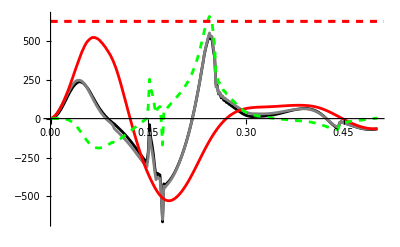

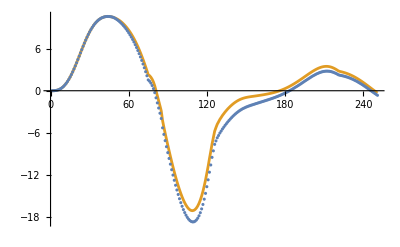

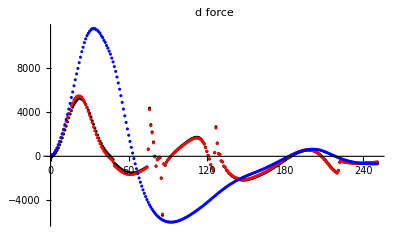

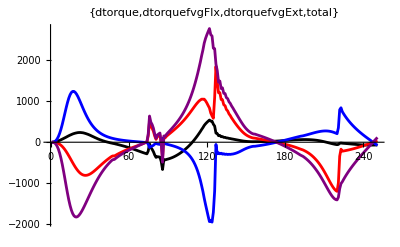

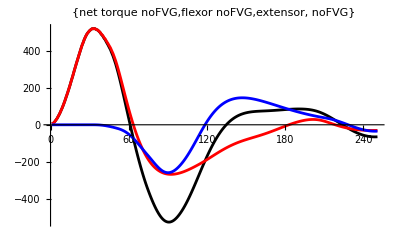

```mathematica
jntindex=1;
prange={-6,10};
flexOrExt=0;(*0 for flex 1 for ext*)
index=(jntindex-1)+jntindex+flexOrExt
adataFlx=actDATA[[;;,index]];
adataExt=actDATA[[;;,index+1]];

flgFlx=flgDATA[[;;,index]];
flgExt=flgDATA[[;;,index+1]];

fvgFlx=fvgDATA[[;;,index]];
fvgExt=fvgDATA[[;;,index+1]];

vdataFlx=velDATA[[;;,index]];
vdataExt=velDATA[[;;,index+1]];

rflx=rValues[[index]];
rext=rValues[[index+1]];

dadataFlx=1*Differentiator1D[adataFlx,mjdt];
dadataExt=1*Differentiator1D[adataExt,mjdt];

dflgFlx=1*Differentiator1D[flgFlx,mjdt];
dflgExt=1*Differentiator1D[flgExt,mjdt];

dfvgFlx=1*Differentiator1D[fvgFlx,mjdt];
dfvgExt=1*Differentiator1D[fvgExt,mjdt];

tqmax=tmaxValues[[jntindex]];
fmaxFlx=fmaxValues[[index]];
fmaxExt=fmaxValues[[index+1]];
(*c=qfrcDATA[[;;,jntindex]];*)
fdataFlx=frcDATA[[;;,index]];
fdataExt=frcDATA[[;;,index+1]];
dfdataFlx=Differentiator1D[fdataFlx,mjdt];
dfdataExt=Differentiator1D[fdataExt,mjdt];

dfdataFlxCal=flgFlx*fvgFlx*dadataFlx+adataFlx*fvgFlx*dflgFlx+adataFlx*flgFlx*dfvgFlx;
dfdataExtCal=flgExt*fvgExt*dadataExt+adataExt*fvgExt*dflgExt+adataExt*flgExt*dfvgExt;

ddataFlxCalnofvg=1*1*dadataFlx+adataFlx*fvgFlx*0+adataFlx*flgFlx*0;
ddataExtCalnofvg=1*1*dadataExt+adataExt*fvgExt*0+adataExt*flgExt*0;

ddataFlxCalnoact=flgFlx*fvgFlx*dadataFlx*0+adataFlx*fvgFlx*dflgFlx*0+adataFlx*flgFlx*dfvgFlx;
ddataExtCalnoact=flgExt*fvgExt*dadataExt*0+adataExt*fvgExt*dflgExt*0+adataExt*flgExt*dfvgExt;

dtorqueCal=fmaxFlx*rflx*dfdataFlxCal-fmaxExt*rext*dfdataExtCal;
Print["dtorque Limits"]
Print["positive dtorque limits: flexor, extensor"]
dtorqueLimitPos={fmaxFlx*rflx*maxActRate,fmaxExt*rext*maxActRate}
Print["negative dtorque limit"]
dtorqueLimitNeg={fmaxFlx*rflx*maxDeactRate-fmaxExt*rext*maxActRate,fmaxExt*rext*maxDeactRate-fmaxFlx*rflx*maxActRate}
dtorqueCaloFVGflx=fmaxFlx*rflx*ddataFlxCalnofvg;
dtorqueCaloFVGext=fmaxExt*rext*ddataExtCalnofvg;
dtorqueCalNoFVG=dtorqueCaloFVGflx-dtorqueCaloFVGext;
dtorqueFVGflx=fmaxFlx*rflx*dfvgFlx;
dtorqueFVGext=fmaxExt*rext*dfvgExt;
dtorqueCalFVG=dtorqueFVGflx-dtorqueFVGext;
dtorqueCalNoACT=fmaxFlx*rflx*ddataFlxCalnoact-fmaxExt*rext*ddataExtCalnoact;
tdata=qfrcDATA[[;;,jntindex]];

dtorque=Differentiator1D[tdata,mjdt];

dtorqueXY=Thread[{timeData,dtorque}];
dtorqueCalXY=Thread[{timeData,dtorqueCal}];
dtorqueCalNoFVGXY=Thread[{timeData,dtorqueCalNoFVG}];
dtorqueCalNoACTXY=Thread[{timeData,dtorqueCalNoACT}];


Show[
ListLinePlot[{dtorqueXY,dtorqueCalXY,dtorqueCalNoFVGXY,dtorqueCalNoACTXY},PlotStyle->{Black,Gray,Red,{Green,Dashed}},PlotRange->All],
ListLinePlot[{{0,dtorqueLimitPos[[1]]},{cutoff,dtorqueLimitPos[[1]]}},PlotStyle->{Red,Dashed}],
ListLinePlot[{{0,dtorqueLimitPos[[2]]},{cutoff,dtorqueLimitPos[[2]]}},PlotStyle->{Red,Dashed}]
]
ListPlot[{fdataFlx*rflx-fdataExt*rext,tdata},Joined->{False,True}]
ListPlot[{dfdataFlx,fmaxFlx*dfdataFlxCal,fmaxFlx*ddataFlxCalnofvg},PlotStyle->{Black,Red,Blue},PlotRange->All,PlotLabel->"d force"]
ListLinePlot[{dtorque,dtorqueFVGflx,dtorqueFVGext,dtorqueCalFVG},PlotRange->All,PlotLabel->{"dtorque","dtorquefvgFlx","dtorquefvgExt","total"},PlotStyle->{Black,Red,Blue,Purple}]
ListLinePlot[{rflx*fmaxFlx*ddataFlxCalnofvg-rext*fmaxExt*ddataExtCalnofvg,rflx*fmaxFlx*ddataFlxCalnofvg,-rflx*fmaxFlx*ddataExtCalnofvg},PlotStyle->{Black,Red,Blue},PlotLabel->{"net torque noFVG","flexor noFVG","extensor, noFVG"}]
```

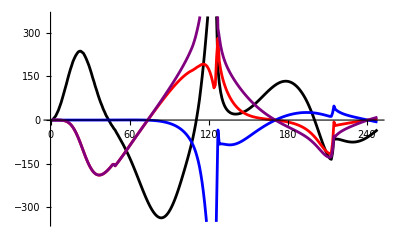

```mathematica
ListLinePlot[{dtorque,fmaxFlx*rflx*ddataFlxCalnoact,fmaxExt*rext*ddataExtCalnoact,dtorqueCalNoACT},PlotStyle->{Black,Red,Blue,Purple}]
```

Perturbation timings
target 0
1: 0.022-0.04
2: 0.064-0.082
3: 0.106-0.124
4: 0.148-0.166

target 1
1: 0.032-0.05
2: 0.094-0.112
3: 0.158-0.176
4: 0.222-0.240

target 2
1: 0.038-0.056
2: 0.116-0.134
3: 0.192-0.210
4: 0.270-0.288

0.112

```mathematica
yrange=(*0.05*)(*0.75*)0.8;
pertTimings={
{"A03_FB_P01_f0",0.022},{"A03_FB_P02_f0",0.064},{"A03_FB_P03_f0",0.106},{"A03_FB_P04_f0",0.148},
{"A03_FB_P01_f1",0.032},{"A03_FB_P02_f1",0.094},{"A03_FB_P03_f1",0.158},{"A03_FB_P04_f1",0.222},
{"A03_FB_P01_f2",0.038},{"A03_FB_P02_f2",0.116},{"A03_FB_P03_f2",0.192},{"A03_FB_P04_f2",0.270}
};
(*perturbation never happens for controls, so make start time arbitrarily large*)
pertTimingsControl={{"A03_FB_P00_f0",10},{"A03_FB_P00_f1",10},{"A03_FB_P00_f2",10}};
pertTimings=Join[pertTimings,pertTimingsControl];
pertStart=pertTimings[[Position[pertTimings,trialname][[1,1]]]][[2]];
pertEnd=pertStart+0.018;

range=1;
ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->Red,Axes->False,Boxed->False];
(*reachAnim=Table*)

Clear[p2,plot1,plot2]
(*animation=Table*)Manipulate[
time=fr*mjdt;
labelnormal=Style[fr*mjdt,Black,15];
labelperturb=Style[fr*mjdt,Red,Bold,20];
label=If[pertStart<=time<=pertEnd,labelperturb,labelnormal];
points=Partition[xyzDATA[[fr]],3];
DATA={shofvDATA2D,elbfvDATA2D,wrifvDATA2D}[[joint]];
p2=Graphics3D[{Thickness[0.007],Line[points]}];
plot1=Show[ptarget,p2,Box->False,ViewPoint->Top,ViewAngle->0.4];
plot2=Show[
DATA[[fr]],
PlotRange->{All,{-yrange,yrange}},PlotStyle->Thick,PlotLabel->label];
GraphicsRow[{plot1,plot2},ImageSize->800]


,{fr,1,Length[shofvDATA2D],1},{joint,1,3,1}]
```

```mathematica
trialname
```

A03_FB_P02_f2

```mathematica
pertTimings
```

{{A03_FB_P01_f0,0.022},{A03_FB_P02_f0,0.064},{A03_FB_P03_f0,0.106},{A03_FB_P04_f0,0.148},{A03_FB_P01_f1,0.032},{A03_FB_P02_f1,0.094},{A03_FB_P03_f1,0.158},{A03_FB_P04_f1,0.222},{A03_FB_P01_f2,0.038},{A03_FB_P02_f2,0.116},{A03_FB_P03_f2,0.192},{A03_FB_P04_f2,0.27}}

```mathematica
SetDirectory[dirreachingSims]
Export[trialname<>"_ELB_2D.mov",animation]
ResetDirectory[]
```

/Users/chris/Desktop/WTageing/CODE/reaching-arm-model-CTR/outputData/setN02_ALL

```mathematica
dirreachingSims
```

/Users/chrisrichards/Desktop/WTageing/DATA/reachingSims/output/setN02_ALL

```mathematica
Dynamic[status]
range=4.5;
pntsize=0.03;
animSize=500;
view1={0.15,{3,2,2},{0.5,0.25,0.5}};(*view angle, view point,view centre*)
view2={0.1,{4,0,0},{.5, 0.33, 0.5}};
view2zoom={0.02,{4,0,0},{0.2,0.5, 0.5}};
(*view2=view2zoom;*)
pntsize=If[view2==view2zoom,0.003,pntsize];
view3={0.15,{-2,2,3},{.5, 0.6, 0.85}};
view3zoom={(*0.15*)0.03,{-2,2,3},{.57, 0.7, 0.85}};
(*view3=view3zoom;*)
view=view1;
plotA=ListPlot3D[{ceilingDATA,floorDATA}(*,Filling->{1->{2}}*),PlotStyle->{{Pink,Opacity[0.7]},{Black,Opacity[0.1]}},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},Boxed->False,Axes->False];
plotB=ListPlot3D[groundplanedata,PlotStyle->{Gray,Opacity[0.1]}];

ptarget=ListPointPlot3D[{targetXYZ},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},PlotStyle->Red,Axes->False,Boxed->False];


Manipulate(*animation=Table*)[
status=fr;
slice=(*fr-1*);;fr;
(*p1=Show[ListPlot3D[{ceilingDATA,floorDATA}(*,Filling->{1->{2}}*),PlotStyle->{{Pink,Opacity[0.7]},{Black,Opacity[0.1]}},PlotRange->Table[{-range,range},{i,1,3}],BoxRatios->{1, 1, 1},Boxed->False,Axes->False],
ListPointPlot3D[shofvDATA[[slice]],PlotStyle->{Black}],
ListPointPlot3D[elbfvDATA[[slice]],PlotStyle->{Red}],
ListPointPlot3D[wrifvDATA[[slice]],PlotStyle->{Blue}],
ListPlot3D[groundplanedata,PlotStyle->{Gray,Opacity[0.1]}],ImageSize->animSize,ViewAngle->view1[[1]],ViewPoint->view1[[2]],ViewCenter->view1[[3]]
];*)

actVectorScaale=0.5;
actLimitDATA={shofvActLimitDATA,elbfvActLimitDATA,wrifvActLimitDATA}[[joint]];
jointDATA={shofvDATA,elbfvDATA,wrifvDATA}[[joint]];
maxActVector=actVectorScaale*Normalize[actLimitDATA[[fr]]-jointDATA[[fr]]];
curActVector=actVectorScaale*Normalize[jointDATA[[fr]]-jointDATA[[fr-1]]];

p2=Show[plotA,
Graphics3D[{Black,Sphere[shofvDATA[[slice]],pntsize]}],
Graphics3D[{Red,Sphere[elbfvDATA[[slice]],pntsize]}],
Graphics3D[{Blue,Sphere[wrifvDATA[[slice]],pntsize]}],
(*Graphics3D[{Green,Sphere[actLimitDATA[[slice]],pntsize]}],
Graphics3D[{Cyan,Thick,Line[{jointDATA[[fr]],jointDATA[[fr]]+maxActVector}]}],
Graphics3D[{Yellow,Thick,Line[{jointDATA[[fr]],jointDATA[[fr]]+curActVector}]}],*)
(*Graphics3D[{Red,Line[{shofvDATA[[fr]],shofvActLimitDATA[[fr]]}]}],*)
plotB,ImageSize->animSize,ViewAngle->view2[[1]],ViewPoint->view2[[2]],ViewCenter->view2[[3]]
];


p3=Show[plotA,
Graphics3D[{Black,Sphere[shofvDATA[[slice]],pntsize]}],
Graphics3D[{Red,Sphere[elbfvDATA[[slice]],pntsize]}],
Graphics3D[{Blue,Sphere[wrifvDATA[[slice]],pntsize]}],
(*Graphics3D[{Green,Sphere[actLimitDATA[[slice]],pntsize]}],
Graphics3D[{Cyan,Thick,Line[{jointDATA[[fr]],jointDATA[[fr]]+maxActVector}]}],
Graphics3D[{Yellow,Thick,Line[{jointDATA[[fr]],jointDATA[[fr]]+curActVector}]}],*)
plotB,ImageSize->animSize,ViewAngle->view3[[1]],ViewPoint->view3[[2]],ViewCenter->view3[[3]]
,PlotLabel->"Time "<>IntegerString[Round[fr*mjdt*1000],10,3]<>" ms",LabelStyle->{Black,FontSize->12}];

armpoints=Partition[xyzDATA[[fr]],3];
plotArm=Graphics3D[{Thickness[0.003],Line[armpoints]}];
plotC=Show[ptarget,plotArm,Box->False,ViewPoint->Top,ViewAngle->0.4,ImageSize->800];

plot=GraphicsRow[{p3,p2},ImageSize->1000(*,Inset[plotC]*)];
Overlay[{plot,plotC},Alignment->Center]

,{fr,2,Length[actDATA],1},{joint,1,3,1}]
animation[[-1]]
```

Part::partd: Part specification animation⟦-1⟧ is longer than depth of object.

animation⟦-1⟧

```mathematica
p2
```

```mathematica
Manipulate[animation[[fr]],{fr,1,Length[animation],1}]
```

```mathematica
.27/mjdt
```

135.

```mathematica
ListPlot[shofvDATA[[;;,3]]]
```

```mathematica
Directory[]
```

/Users/chrisrichards

```mathematica
SetDirectory[dirreachingSims]
Export[trialname<>"_rescaled.mov",animation]
ResetDirectory[]
```

/Users/chrisrichards/Desktop/WTageing/DATA/reachingSims/output/setN02_ALL

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

A03_FB_P00_s1_rescaled.mov

/Users/chrisrichards/Desktop/WTageing/DATA/reachingSims/output/setN02_ALL

```mathematica
SetDirectory[dirreachingSims]
Export[trialname<>".png",figurePlot]
ResetDirectory[]
```

/Users/chrisrichards/Desktop/WTageing/DATA/reachingSims/output/setN02_ALL

A03_FB_P00_s0.png

/Users/chrisrichards

```mathematica
dirreachingSims
```

/Users/chrisrichards/Desktop/WTageing/DATA/reachingSims/output/setN02_ALL

```mathematica
actDATA1==actDATA2
```

True

```mathematica
DDATA
```

{1,2}